```mathematica
SetDirectory[NotebookDirectory[]];
Get["betas.m"];
```

Huge notebook where both parametric and theoretical uncertainty is calculated, as well as final plots drawn

## Parametric uncertainty

```mathematica
loopCofigs={{1,1,1,1,1,1},{2,2,2,2,2,2},{3,3,3,3,3,3},{3,3,3,2,2,1},{4,4,4,3,3,2},{4,4,4,3,3,3}}
```

{{1,1,1,1,1,1},{2,2,2,2,2,2},{3,3,3,3,3,3},{3,3,3,2,2,1},{4,4,4,3,3,2},{4,4,4,3,3,3}}

```mathematica
(*obtained by propogation of errors after fit.cpp, of form x1 x2 x3 y1 y2 z*)
means[1,1,1,1,1,1]={5/(48Pi^2)0.358487^2,1/(16Pi^2)0.648175^2,1/(16Pi^2)1.16423^2,1/(16Pi^2)0.991191^2,1/(16Pi^2)0.0167928^2,1/(16Pi^2)0.129281};
sigmas[1,1,1,1,1,1]={1.28442*^-07,1.84023*^-07, 5.97428*^-05, 2.09102*^-05, 1.42843*^-08, 1.43857*^-06};
means[2,2,2,2,2,2]={5/(48Pi^2)0.358635^2,1/(16Pi^2)0.647391^2,1/(16Pi^2)1.16455^2,1/(16Pi^2)0.946186^2,1/(16Pi^2)0.0167643^2,1/(16Pi^2)0.126844};
sigmas[2,2,2,2,2,2]={1.30313*^-07,2.11039*^-07, 5.98399*^-05, 2.08587*^-05, 1.42303*^-08, 1.44297*^-06};means[3,3,3,3,3,3]={5/(48Pi^2)0.358594^2,1/(16Pi^2)0.647628^2,1/(16Pi^2)1.16312^2,1/(16Pi^2)0.935618^2,1/(16Pi^2)0.0156334^2,1/(16Pi^2)0.126309};
sigmas[3,3,3,3,3,3]={1.29848*^-07,1.69515*^-07, 5.93997*^-05, 2.0995*^-05, 1.69777*^-08, 1.43662*^-06};means[3,3,3,2,2,1]={5/(48Pi^2)0.358357^2,1/(16Pi^2)0.649037^2,1/(16Pi^2)1.16312^2,1/(16Pi^2)0.937029^2,1/(16Pi^2)0.0168134^2,1/(16Pi^2)0.129281};
sigmas[3,3,3,2,2,1]={1.3315*^-07,2.70841*^-07, 5.93998*^-05, 2.12139*^-05, 1.42037*^-08, 1.43857*^-06};
means[4,4,4,3,3,2]={5/(48Pi^2)0.358609^2,1/(16Pi^2)0.64754^2,1/(16Pi^2)1.16316^2,1/(16Pi^2)0.932712^2,1/(16Pi^2)0.0156331^2,1/(16Pi^2)0.126631};
sigmas[4,4,4,3,3,2]={1.30197*^-07,2.0914*^-07, 5.94267*^-05,2.11114*^-05, 1.69782*^-08, 1.43659*^-06};
means[4,4,4,3,3,3]={5/(48Pi^2)0.358604^2,1/(16Pi^2)0.64757^2,1/(16Pi^2)1.16316^2,1/(16Pi^2)0.932746^2,1/(16Pi^2)0.0156336^2,1/(16Pi^2)0.126274};
sigmas[4,4,4,3,3,3]={1.29891*^-07,2.04007*^-07, 5.94267*^-05,2.1125*^-05,1.69789*^-08, 1.44158*^-06};
```

```mathematica
Table[{i,Around[means[1,1,1,1,1,1][[i]],sigmas[1,1,1,1,1,1][[i]]],Around[means[2,2,2,2,2,2][[i]],sigmas[2,2,2,2,2,2][[i]]],Around[means[3,3,3,3,3,3][[i]],sigmas[3,3,3,3,3,3][[i]]]},{i,1,6}]//TeXForm
```

\left(
\begin{array}{cccc}
 1 & 0.001356@! @! @! (36\! \pm \! 13@! ) & 0.001357@! @! @! (48\! \pm \! 13@! ) & 0.001357@! @! @! (17\! \pm \! 13@! ) \\
 2 & 0.002660@! @! @! (51\! \pm \! 18@! ) & 0.002654@! @! @! (08\! \pm \! 21@! ) & 0.002656@! @! @! (02\! \pm \! 17@! ) \\
 3 & 0.00858\pm 0.00006 & 0.00859\pm 0.00006 & 0.00857\pm 0.00006 \\
 4 & 0.006221\pm 0.000021 & 0.005669\pm 0.000021 & 0.005543\pm 0.000021 \\
 5 & (1.786\pm 0.014)\times 10^{-6} & (1.780\pm 0.014)\times 10^{-6} & (1.548\pm 0.017)\times 10^{-6} \\
 6 & 0.00081@! @! @! (87\! \pm \! 14@! ) & 0.00080@! @! @! (32\! \pm \! 14@! ) & 0.00079@! @! @! (99\! \pm \! 14@! ) \\
\end{array}
\right)

```mathematica
Table[{i,Around[means[3,3,3,2,2,1][[i]],sigmas[3,3,3,2,2,1][[i]]],Around[means[4,4,4,3,3,2][[i]],sigmas[4,4,4,3,3,2][[i]]],Around[means[4,4,4,3,3,3][[i]],sigmas[4,4,4,3,3,3][[i]]]},{i,1,6}]//TeXForm
```

\left(
\begin{array}{cccc}
 1 & 0.001355@! @! @! (38\! \pm \! 13@! ) & 0.001357@! @! @! (29\! \pm \! 13@! ) & 0.001357@! @! @! (25\! \pm \! 13@! ) \\
 2 & 0.002667@! @! @! (59\! \pm \! 27@! ) & 0.002655@! @! @! (30\! \pm \! 21@! ) & 0.002655@! @! @! (55\! \pm \! 20@! ) \\
 3 & 0.00857\pm 0.00006 & 0.00857\pm 0.00006 & 0.00857\pm 0.00006 \\
 4 & 0.005560\pm 0.000021 & 0.005509\pm 0.000021 & 0.005509\pm 0.000021 \\
 5 & (1.790\pm 0.014)\times 10^{-6} & (1.548\pm 0.017)\times 10^{-6} & (1.548\pm 0.017)\times 10^{-6} \\
 6 & 0.00081@! @! @! (87\! \pm \! 14@! ) & 0.00080@! @! @! (19\! \pm \! 14@! ) & 0.00079@! @! @! (96\! \pm \! 14@! ) \\
\end{array}
\right)

```mathematica
centralSol[loops_]:=NDSolve[
{x1'[t]==((x1dot@@loops)/.{x1->x1[t],x2->x2[t],x3->x3[t],y1->y1[t],y2->y2[t],z->z[t]}),x2'[t]==((x2dot@@loops)/.{x1->x1[t],x2->x2[t],x3->x3[t],y1->y1[t],y2->y2[t],z->z[t]}),x3'[t]==((x3dot@@loops)/.{x1->x1[t],x2->x2[t],x3->x3[t],y1->y1[t],y2->y2[t],z->z[t]}),y1'[t]==((y1dot@@loops)/.{x1->x1[t],x2->x2[t],x3->x3[t],y1->y1[t],y2->y2[t],z->z[t]}),y2'[t]==((y2dot@@loops)/.{x1->x1[t],x2->x2[t],x3->x3[t],y1->y1[t],y2->y2[t],z->z[t]}),z'[t]==((zdot@@loops)/.{x1->x1[t],x2->x2[t],x3->x3[t],y1->y1[t],y2->y2[t],z->z[t]}), 
x1[0]==(means@@loops)[[1]],x2[0]==(means@@loops)[[2]],x3[0]==(means@@loops)[[3]],y1[0]==(means@@loops)[[4]],y2[0]==(means@@loops)[[5]],z[0]==(means@@loops)[[6]]}
,{x1[t],x2[t],x3[t],y1[t],y2[t],z[t]},
{t,0,100}][[1,6,2]];
```

```mathematica
generateRandomRG[n_, loops_]:=
(
currentLoop = loops;
Table[
processed = i;
NDSolve[
{x1'[t]==((x1dot@@loops)/.{x1->x1[t],x2->x2[t],x3->x3[t],y1->y1[t],y2->y2[t],z->z[t]}),x2'[t]==((x2dot@@loops)/.{x1->x1[t],x2->x2[t],x3->x3[t],y1->y1[t],y2->y2[t],z->z[t]}),x3'[t]==((x3dot@@loops)/.{x1->x1[t],x2->x2[t],x3->x3[t],y1->y1[t],y2->y2[t],z->z[t]}),y1'[t]==((y1dot@@loops)/.{x1->x1[t],x2->x2[t],x3->x3[t],y1->y1[t],y2->y2[t],z->z[t]}),y2'[t]==((y2dot@@loops)/.{x1->x1[t],x2->x2[t],x3->x3[t],y1->y1[t],y2->y2[t],z->z[t]}),z'[t]==((zdot@@loops)/.{x1->x1[t],x2->x2[t],x3->x3[t],y1->y1[t],y2->y2[t],z->z[t]}), 
x1[0]==RandomVariate[NormalDistribution[(means@@loops)[[1]],(sigmas@@loops)[[1]]]],x2[0]==RandomVariate[NormalDistribution[(means@@loops)[[2]],(sigmas@@loops)[[2]]]],x3[0]==RandomVariate[NormalDistribution[(means@@loops)[[3]],(sigmas@@loops)[[3]]]],y1[0]==RandomVariate[NormalDistribution[(means@@loops)[[4]],(sigmas@@loops)[[4]]]],y2[0]==RandomVariate[NormalDistribution[(means@@loops)[[5]],(sigmas@@loops)[[5]]]],z[0]==RandomVariate[NormalDistribution[(means@@loops)[[6]],(sigmas@@loops)[[6]]]]}
,{x1[t],x2[t],x3[t],y1[t],y2[t],z[t]},
{t,0,100}][[1,6]]
,{i,1,n}]
)
```

epic coming

```mathematica
Dynamic[currentLoop]
```

```mathematica
Dynamic[processed]
```

```mathematica
numberLines = 10;
```

```mathematica
(*generate curves*)
sols[1,1,1,1,1,1]=generateRandomRG[numberLines,{1,1,1,1,1,1}];
sols[2,2,2,2,2,2]=generateRandomRG[numberLines,{2,2,2,2,2,2}];
sols[3,3,3,3,3,3]=generateRandomRG[numberLines,{3,3,3,3,3,3}];
sols[3,3,3,2,2,1]=generateRandomRG[numberLines,{3,3,3,2,2,1}];
sols[4,4,4,3,3,2]=generateRandomRG[numberLines,{4,4,4,3,3,2}];
sols[4,4,4,3,3,3]=generateRandomRG[numberLines,{4,4,4,3,3,3}];
```

```mathematica
(*calculate zeros and minima*)
{roots[1,1,1,1,1,1], mins[1,1,1,1,1,1], tofmins[1,1,1,1,1,1]}=
Transpose@Table[
If[Length@#==0,#,#[[2]]]&/@(Flatten@{FindRoot[sols[1,1,1,1,1,1][[i,2]],{t,30}][[1,2]],FindMinimum[{sols[1,1,1,1,1,1][[i,2]],10<=t<=80},{t,60}]})
,{i,1,Length[sols[1,1,1,1,1,1]]}];
{roots[2,2,2,2,2,2], mins[2,2,2,2,2,2], tofmins[2,2,2,2,2,2]}=
Transpose@Table[
If[Length@#==0,#,#[[2]]]&/@(Flatten@{FindRoot[sols[2,2,2,2,2,2][[i,2]],{t,35}][[1,2]],FindMinimum[{sols[2,2,2,2,2,2][[i,2]],10<=t<=80},{t,60}]})
,{i,1,Length[sols[2,2,2,2,2,2]]}];
{roots[3,3,3,3,3,3], mins[3,3,3,3,3,3], tofmins[3,3,3,3,3,3]}=
Transpose@Table[
If[Length@#==0,#,#[[2]]]&/@(Flatten@{FindRoot[sols[3,3,3,3,3,3][[i,2]],{t,35}][[1,2]],FindMinimum[{sols[3,3,3,3,3,3][[i,2]],10<=t<=80},{t,60}]})
,{i,1,Length[sols[3,3,3,3,3,3]]}];
{roots[4,4,4,3,3,3], mins[4,4,4,3,3,3], tofmins[4,4,4,3,3,3]}=
Transpose@Table[
If[Length@#==0,#,#[[2]]]&/@(Flatten@{FindRoot[sols[4,4,4,3,3,3][[i,2]],{t,35}][[1,2]],FindMinimum[{sols[4,4,4,3,3,3][[i,2]],10<=t<=80},{t,60}]})
,{i,1,Length[sols[4,4,4,3,3,3]]}];
{roots[3,3,3,2,2,1], mins[3,3,3,2,2,1], tofmins[3,3,3,2,2,1]}=
Transpose@Table[
If[Length@#==0,#,#[[2]]]&/@(Flatten@{FindRoot[sols[3,3,3,2,2,1][[i,2]],{t,35}][[1,2]],FindMinimum[{sols[3,3,3,2,2,1][[i,2]],10<=t<=80},{t,60}]})
,{i,1,Length[sols[3,3,3,2,2,1]]}];
{roots[4,4,4,3,3,2], mins[4,4,4,3,3,2], tofmins[4,4,4,3,3,2]}=
Transpose@Table[
If[Length@#==0,#,#[[2]]]&/@(Flatten@{FindRoot[sols[4,4,4,3,3,2][[i,2]],{t,35}][[1,2]],FindMinimum[{sols[4,4,4,3,3,2][[i,2]],10<=t<=80},{t,60}]})
,{i,1,Length[sols[4,4,4,3,3,2]]}];
```

```mathematica
(*load data already calculated*)
solsDataSofar = Import["C:\Users\mrgeb\OneDrive\Documents\вольфрам стафф\sols_data_sofar.dat"];

roots[1,1,1,1,1,1] = Join[roots[1,1,1,1,1,1], solsDataSofar[[1]]];
mins[1,1,1,1,1,1] = Join[mins[1,1,1,1,1,1], solsDataSofar[[2]]];
tofmins[1,1,1,1,1,1] = Join[tofmins[1,1,1,1,1,1], solsDataSofar[[3]]];

roots[2,2,2,2,2,2] = Join[roots[2,2,2,2,2,2], solsDataSofar[[4]]];
mins[2,2,2,2,2,2] = Join[mins[2,2,2,2,2,2], solsDataSofar[[5]]];
tofmins[2,2,2,2,2,2] = Join[tofmins[2,2,2,2,2,2], solsDataSofar[[6]]];

roots[3,3,3,3,3,3] = Join[roots[3,3,3,3,3,3], solsDataSofar[[7]]];
mins[3,3,3,3,3,3] = Join[mins[3,3,3,3,3,3], solsDataSofar[[8]]];
tofmins[3,3,3,3,3,3] = Join[tofmins[3,3,3,3,3,3], solsDataSofar[[9]]];

roots[4,4,4,3,3,3] = Join[roots[4,4,4,3,3,3], solsDataSofar[[10]]];
mins[4,4,4,3,3,3] = Join[mins[4,4,4,3,3,3], solsDataSofar[[11]]];
tofmins[4,4,4,3,3,3] = Join[tofmins[4,4,4,3,3,3], solsDataSofar[[12]]];

roots[3,3,3,2,2,1] = Join[roots[3,3,3,2,2,1], solsDataSofar[[13]]];
mins[3,3,3,2,2,1] = Join[mins[3,3,3,2,2,1], solsDataSofar[[14]]];
tofmins[3,3,3,2,2,1] = Join[tofmins[3,3,3,2,2,1], solsDataSofar[[15]]];

roots[4,4,4,3,3,2] = Join[roots[4,4,4,3,3,2], solsDataSofar[[16]]];
mins[4,4,4,3,3,2] = Join[mins[4,4,4,3,3,2], solsDataSofar[[17]]];
tofmins[4,4,4,3,3,2] = Join[tofmins[4,4,4,3,3,2], solsDataSofar[[18]]];
```

```mathematica
(*check how many curves we have*)
Length[roots[4,4,4,3,3,2]]
```

510

```mathematica
(*means and uncs*)
theRoot[1,1,1,1,1,1] = Around[FindRoot[centralSol[{1,1,1,1,1,1}],{t,30}][[1,2]],StandardDeviation[roots[1,1,1,1,1,1]]];
theMin[1,1,1,1,1,1] = Around[FindMinimum[{centralSol[{1,1,1,1,1,1}],10<=t<=80},{t,60}][[1]],StandardDeviation[mins[1,1,1,1,1,1]]];
theTofMin[1,1,1,1,1,1]=Around[FindMinimum[{centralSol[{1,1,1,1,1,1}],10<=t<=80},{t,60}][[2,1,2]],StandardDeviation[tofmins[1,1,1,1,1,1]]];

theRoot[2,2,2,2,2,2] = Around[FindRoot[centralSol[{2,2,2,2,2,2}],{t,30}][[1,2]],StandardDeviation[roots[2,2,2,2,2,2]]];
theMin[2,2,2,2,2,2] = Around[FindMinimum[{centralSol[{2,2,2,2,2,2}],10<=t<=80},{t,60}][[1]],StandardDeviation[mins[2,2,2,2,2,2]]];
theTofMin[2,2,2,2,2,2]=Around[FindMinimum[{centralSol[{2,2,2,2,2,2}],10<=t<=80},{t,60}][[2,1,2]],StandardDeviation[tofmins[2,2,2,2,2,2]]];

theRoot[3,3,3,3,3,3] = Around[FindRoot[centralSol[{3,3,3,3,3,3}],{t,30}][[1,2]],StandardDeviation[roots[3,3,3,3,3,3]]];
theMin[3,3,3,3,3,3] = Around[FindMinimum[{centralSol[{3,3,3,3,3,3}],10<=t<=80},{t,60}][[1]],StandardDeviation[mins[3,3,3,3,3,3]]];
theTofMin[3,3,3,3,3,3]=Around[FindMinimum[{centralSol[{3,3,3,3,3,3}],10<=t<=80},{t,60}][[2,1,2]],StandardDeviation[tofmins[3,3,3,3,3,3]]];

theRoot[3,3,3,2,2,1] = Around[FindRoot[centralSol[{3,3,3,2,2,1}],{t,30}][[1,2]],StandardDeviation[roots[3,3,3,2,2,1]]];
theMin[3,3,3,2,2,1] = Around[FindMinimum[{centralSol[{3,3,3,2,2,1}],10<=t<=80},{t,60}][[1]],StandardDeviation[mins[3,3,3,2,2,1]]];
theTofMin[3,3,3,2,2,1]=Around[FindMinimum[{centralSol[{3,3,3,2,2,1}],10<=t<=80},{t,60}][[2,1,2]],StandardDeviation[tofmins[3,3,3,2,2,1]]];

theRoot[4,4,4,3,3,2] = Around[FindRoot[centralSol[{4,4,4,3,3,2}],{t,30}][[1,2]],StandardDeviation[roots[4,4,4,3,3,2]]];
theMin[4,4,4,3,3,2] = Around[FindMinimum[{centralSol[{4,4,4,3,3,2}],10<=t<=80},{t,60}][[1]],StandardDeviation[mins[4,4,4,3,3,2]]];
theTofMin[4,4,4,3,3,2]=Around[FindMinimum[{centralSol[{4,4,4,3,3,2}],10<=t<=80},{t,60}][[2,1,2]],StandardDeviation[tofmins[4,4,4,3,3,2]]];

theRoot[4,4,4,3,3,3] = Around[FindRoot[centralSol[{4,4,4,3,3,3}],{t,30}][[1,2]],StandardDeviation[roots[4,4,4,3,3,3]]];
theMin[4,4,4,3,3,3] = Around[FindMinimum[{centralSol[{4,4,4,3,3,3}],10<=t<=80},{t,60}][[1]],StandardDeviation[mins[4,4,4,3,3,3]]];
theTofMin[4,4,4,3,3,3]=Around[FindMinimum[{centralSol[{4,4,4,3,3,3}],10<=t<=80},{t,60}][[2,1,2]],StandardDeviation[tofmins[4,4,4,3,3,3]]];
```

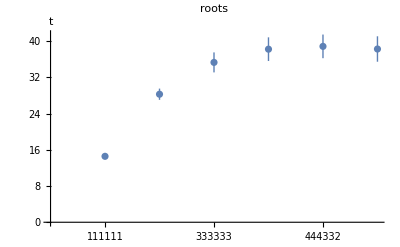

```mathematica
ListPlot[{{1,theRoot[1,1,1,1,1,1]},{2,theRoot[2,2,2,2,2,2]},{3, theRoot[3,3,3,3,3,3]},{4,theRoot[3,3,3,2,2,1]},{5,theRoot[4,4,4,3,3,2]},{6,theRoot[4,4,4,3,3,3]}},Ticks->{{{1,"111111"},{2,"222222"},{3,"333333"},{4,"333221"},{5,"444332"},{6,"444333"}},Automatic},PlotLabel->"roots", AxesLabel->{None,"t"}]
```

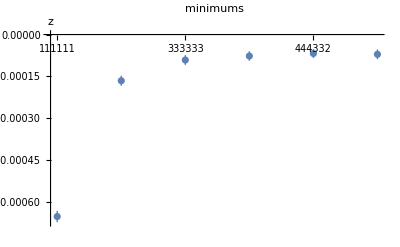

```mathematica
ListPlot[{{1,theMin[1,1,1,1,1,1]},{2,theMin[2,2,2,2,2,2]},{3, theMin[3,3,3,3,3,3]},{4,theMin[3,3,3,2,2,1]},{5,theMin[4,4,4,3,3,2]},{6,theMin[4,4,4,3,3,3]}},Ticks->{{{1,"111111"},{2,"222222"},{3,"333333"},{4,"333221"},{5,"444332"},{6,"444333"}},Automatic},PlotLabel->"minimums", AxesLabel->{None,"z"},PlotRange->Full]
```

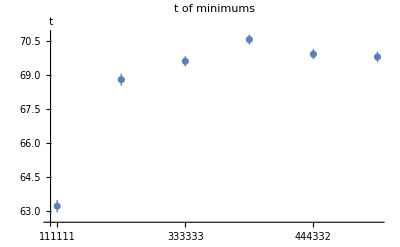

```mathematica
ListPlot[{{1,theTofMin[1,1,1,1,1,1]},{2,theTofMin[2,2,2,2,2,2]},{3, theTofMin[3,3,3,3,3,3]},{4,theTofMin[3,3,3,2,2,1]},{5,theTofMin[4,4,4,3,3,2]},{6,theTofMin[4,4,4,3,3,3]}},Ticks->{{{1,"111111"},{2,"222222"},{3,"333333"},{4,"333221"},{5,"444332"},{6,"444333"}},Automatic},PlotLabel->"t of minimums", AxesLabel->{None,"t"},PlotRange->Full]
```

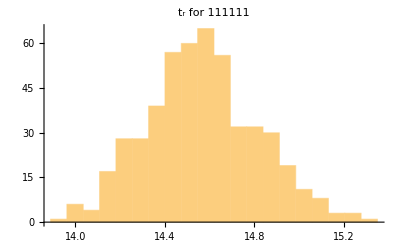

```mathematica
Histogram[roots[1,1,1,1,1,1],{"Raw",20},PlotLabel->"t_r for 111111"]
Export["figures/exampleofroots.pdf",%]
```

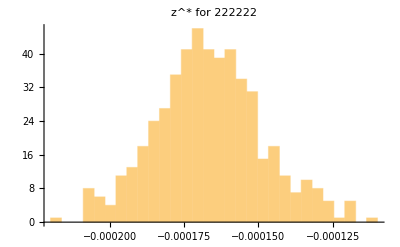

```mathematica
Histogram[mins[2,2,2,2,2,2],{"Raw",30},PlotLabel->"z^* for 222222"]
Export["figures/exampleofmins.pdf",%]
```

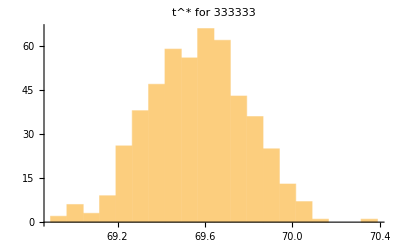

```mathematica
Histogram[tofmins[3,3,3,3,3,3],{"Raw",20},PlotLabel->"t^* for 333333"]
Export["figures/exampleoftofmins.pdf",%]
```

```mathematica
muTOt[μ_]:=2Log[μ/173.22]
tTOmu[t_]:=173.22*Exp[t/2]
tTOmuWErrors[t_Around]:=Around[tTOmu[t[[1]]],{tTOmu[t[[1]]]-tTOmu[t[[1]]-t[[2]]],tTOmu[t[[1]]+t[[2]]]-tTOmu[t[[1]]]}]
```

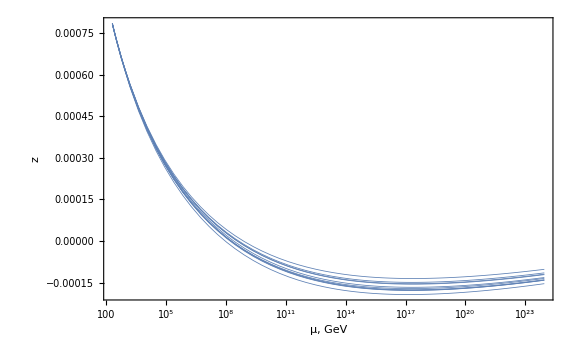

```mathematica
LogLinearPlot[Table[z[t]/.sols[2,2,2,2,2,2][[i]],{i,1,10}]/.{t->muTOt[μ]},{μ,200,9*^23},PlotStyle->Thickness[0.001],PlotRange->Full,FrameTicks -> {{Automatic,Automatic}, {Automatic, None}},  FrameLabel -> {"μ, GeV", "z"}, Frame -> True, 
 LabelStyle -> {FontSize -> 18, FontFamily -> "Times"},ImageSize->Large]
Export["figures/exampleofrandom.pdf",%]
```

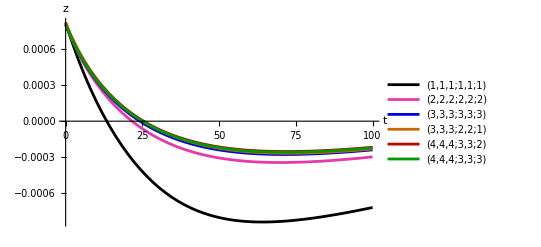

```mathematica
drawSolutions[Table[{loopCofigs[[i]],means@@loopCofigs[[i]]},{i,1,6}],{0,100}]
```

```mathematica
Export["sols_data_sofar.dat",{roots[1,1,1,1,1,1], mins[1,1,1,1,1,1], tofmins[1,1,1,1,1,1],roots[2,2,2,2,2,2], mins[2,2,2,2,2,2], tofmins[2,2,2,2,2,2],roots[3,3,3,3,3,3], mins[3,3,3,3,3,3], tofmins[3,3,3,3,3,3],roots[4,4,4,3,3,3], mins[4,4,4,3,3,3], tofmins[4,4,4,3,3,3],roots[3,3,3,2,2,1], mins[3,3,3,2,2,1], tofmins[3,3,3,2,2,1],roots[4,4,4,3,3,2], mins[4,4,4,3,3,2], tofmins[4,4,4,3,3,2]}]
```

C:\Users\mrgeb\OneDrive\Documents\вольфрам стафф\sols_data_sofar.dat

```mathematica
solsDataSofar = Import["sols_data_sofar.dat"];
Length[solsDataSofar[[-1]]]
```

500

```mathematica
epic={{theRoot[1,1,1,1,1,1],theRoot[2,2,2,2,2,2],theRoot[3,3,3,3,3,3],theRoot[3,3,3,2,2,1],theRoot[4,4,4,3,3,2],theRoot[4,4,4,3,3,3]},{theMin[1,1,1,1,1,1],theMin[2,2,2,2,2,2],theMin[3,3,3,3,3,3],theMin[3,3,3,2,2,1],theMin[4,4,4,3,3,2],theMin[4,4,4,3,3,3]},{theTofMin[1,1,1,1,1,1],theTofMin[2,2,2,2,2,2],theTofMin[3,3,3,3,3,3],theTofMin[3,3,3,2,2,1],theTofMin[4,4,4,3,3,2],theTofMin[4,4,4,3,3,3]}};
epic // TableForm
epic//TeXForm
```

13.40.5 | 21.71.3 | 24.31.6 | 25.41.7 | 25.41.8 | 25.11.7
-0.000840.00004 | -0.000340.00004 | -0.0002750.000035 | -0.000260.00004 | -0.000250.00004 | -0.0002580.000035
64.10.6 | 69.40.9 | 71.10.9 | 72.10.7 | 71.60.8 | 71.50.8

\left(
\begin{array}{cccccc}
 13.4\pm 0.5 & 21.7\pm 1.3 & 24.3\pm 1.6 & 25.4\pm 1.7 & 25.4\pm 1.8 & 25.1\pm 1.7 \\
 -0.00084\pm 0.00004 & -0.00034\pm 0.00004 & -0.000275\pm 0.000035 & -0.00026\pm 0.00004 & -0.00025\pm 0.00004 & -0.000258\pm 0.000035 \\
 64.1\pm 0.6 & 69.4\pm 0.9 & 71.1\pm 0.9 & 72.1\pm 0.7 & 71.6\pm 0.8 & 71.5\pm 0.8 \\
\end{array}
\right)

## Theoretical uncertainty

```mathematica
loopCofigs={{1,1,1,1,1,1},{2,2,2,2,2,2},{3,3,3,3,3,3},{3,3,3,2,2,1},{4,4,4,3,3,2},{4,4,4,3,3,3}}
```

{{1,1,1,1,1,1},{2,2,2,2,2,2},{3,3,3,3,3,3},{3,3,3,2,2,1},{4,4,4,3,3,2},{4,4,4,3,3,3}}

```mathematica
runto0[Q_,x1i_,x2i_,x3i_,y1i_,y2i_,zi_,loops_]:=Join[{Q},NDSolve[
{x1'[t]==((x1dot@@loops)/.{x1->x1[t],x2->x2[t],x3->x3[t],y1->y1[t],y2->y2[t],z->z[t]}),x2'[t]==((x2dot@@loops)/.{x1->x1[t],x2->x2[t],x3->x3[t],y1->y1[t],y2->y2[t],z->z[t]}),x3'[t]==((x3dot@@loops)/.{x1->x1[t],x2->x2[t],x3->x3[t],y1->y1[t],y2->y2[t],z->z[t]}),y1'[t]==((y1dot@@loops)/.{x1->x1[t],x2->x2[t],x3->x3[t],y1->y1[t],y2->y2[t],z->z[t]}),y2'[t]==((y2dot@@loops)/.{x1->x1[t],x2->x2[t],x3->x3[t],y1->y1[t],y2->y2[t],z->z[t]}),z'[t]==((zdot@@loops)/.{x1->x1[t],x2->x2[t],x3->x3[t],y1->y1[t],y2->y2[t],z->z[t]}), 
x1[Log[Q^2/173.22^2]]==x1i,x2[Log[Q^2/173.22^2]]==x2i,x3[Log[Q^2/173.22^2]]==x3i,y1[Log[Q^2/173.22^2]]==y1i,y2[Log[Q^2/173.22^2]]==y2i,z[Log[Q^2/173.22^2]]==zi}
,{x1[t],x2[t],x3[t],y1[t],y2[t],z[t]},
{t,-10,10}][[1, All, 2]]/.{t->0}]
```

```mathematica
runto0[84.61, 0.00134977,0.00266446, 0.00944086,0.0062215,1.9944*^-6, 0.000818679,{1,1,1,1,1,1}]
```

{84.61,0.00136056,0.00263263,0.00862414,0.00577217,1.80543×10^-6,0.00070622}

```mathematica
(*obtained by theorerr.cpp*)
theorerr={"|1,1,1|1,1|1|",runto0[86.6151,0.00134977,0.00266446,0.00936873,0.0062215,1.99609*^-6,0.000818679,{1,1,1,1,1,1}],runto0[90.7111,0.00135021,0.0026642,0.0093119,0.0062215,1.98083*^-6,0.000818679,{1,1,1,1,1,1}],runto0[95.0009,0.00135065,0.00266393,0.00925576,0.0062215,1.96576*^-6,0.000818679,{1,1,1,1,1,1}],runto0[99.4935,0.00135109,0.00266367,0.0092003,0.0062215,1.95088*^-6,0.000818679,{1,1,1,1,1,1}],runto0[104.199,0.00135153,0.00266341,0.0091455,0.0062215,1.93618*^-6,0.000818679,{1,1,1,1,1,1}],runto0[109.126,0.00135196,0.00266314,0.00909135,0.0062215,1.92167*^-6,0.000818679,{1,1,1,1,1,1}],runto0[114.287,0.0013524,0.00266288,0.00903785,0.0062215,1.90733*^-6,0.000818679,{1,1,1,1,1,1}],runto0[119.691,0.00135284,0.00266262,0.00898497,0.0062215,1.89317*^-6,0.000818679,{1,1,1,1,1,1}],runto0[125.351,0.00135328,0.00266235,0.00893271,0.0062215,1.87918*^-6,0.000818679,{1,1,1,1,1,1}],runto0[131.279,0.00135372,0.00266209,0.00888105,0.0062215,1.86535*^-6,0.000818679,{1,1,1,1,1,1}],runto0[137.488,0.00135416,0.00266183,0.00883,0.0062215,1.85169*^-6,0.000818679,{1,1,1,1,1,1}],runto0[143.989,0.0013546,0.00266156,0.00877952,0.0062215,1.8382*^-6,0.000818679,{1,1,1,1,1,1}],runto0[150.799,0.00135504,0.0026613,0.00872963,0.0062215,1.82486*^-6,0.000818679,{1,1,1,1,1,1}],runto0[157.93,0.00135548,0.00266104,0.0086803,0.0062215,1.81168*^-6,0.000818679,{1,1,1,1,1,1}],runto0[165.398,0.00135592,0.00266077,0.00863153,0.0062215,1.79865*^-6,0.000818679,{1,1,1,1,1,1}],runto0[173.22,0.00135636,0.00266051,0.0085833,0.0062215,1.78578*^-6,0.000818679,{1,1,1,1,1,1}],runto0[181.412,0.0013568,0.00266024,0.00853561,0.0062215,1.77306*^-6,0.000818679,{1,1,1,1,1,1}],runto0[189.991,0.00135724,0.00265998,0.00848845,0.0062215,1.76048*^-6,0.000818679,{1,1,1,1,1,1}],runto0[198.975,0.00135768,0.00265971,0.00844182,0.0062215,1.74804*^-6,0.000818679,{1,1,1,1,1,1}],runto0[208.385,0.00135812,0.00265945,0.00839569,0.0062215,1.73575*^-6,0.000818679,{1,1,1,1,1,1}],runto0[218.239,0.00135856,0.00265919,0.00835007,0.0062215,1.7236*^-6,0.000818679,{1,1,1,1,1,1}],runto0[228.56,0.001359,0.00265892,0.00830494,0.0062215,1.71158*^-6,0.000818679,{1,1,1,1,1,1}],runto0[239.368,0.00135945,0.00265866,0.0082603,0.0062215,1.6997*^-6,0.000818679,{1,1,1,1,1,1}],runto0[250.688,0.00135989,0.00265839,0.00821613,0.0062215,1.68795*^-6,0.000818679,{1,1,1,1,1,1}],runto0[262.543,0.00136033,0.00265813,0.00817244,0.0062215,1.67633*^-6,0.000818679,{1,1,1,1,1,1}],runto0[274.959,0.00136077,0.00265786,0.00812922,0.0062215,1.66485*^-6,0.000818679,{1,1,1,1,1,1}],runto0[287.962,0.00136121,0.0026576,0.00808645,0.0062215,1.65348*^-6,0.000818679,{1,1,1,1,1,1}],runto0[301.579,0.00136166,0.00265733,0.00804413,0.00622151,1.64224*^-6,0.000818679,{1,1,1,1,1,1}],runto0[315.841,0.0013621,0.00265706,0.00800225,0.00622151,1.63113*^-6,0.000818679,{1,1,1,1,1,1}],runto0[330.777,0.00136254,0.0026568,0.0079608,0.00622151,1.62013*^-6,0.000818679,{1,1,1,1,1,1}],runto0[346.42,0.00136298,0.00265653,0.00791979,0.00622151,1.60926*^-6,0.000818679,{1,1,1,1,1,1}],"|2,2,2|2,2|2|",runto0[86.6151,0.00134607,0.00268952,0.00936892,0.00608237,1.95675*^-6,0.000917378,{2,2,2,2,2,2}],runto0[90.7111,0.00134685,0.00268697,0.00931247,0.00605291,1.94403*^-6,0.000908631,{2,2,2,2,2,2}],runto0[95.0009,0.00134763,0.00268445,0.00925671,0.00602374,1.93145*^-6,0.00090006,{2,2,2,2,2,2}],runto0[99.4935,0.0013484,0.00268196,0.0092016,0.00599486,1.91901*^-6,0.000891664,{2,2,2,2,2,2}],runto0[104.199,0.00134917,0.00267949,0.00914715,0.00596627,1.9067*^-6,0.000883436,{2,2,2,2,2,2}],runto0[109.126,0.00134994,0.00267706,0.00909334,0.00593795,1.89453*^-6,0.000875376,{2,2,2,2,2,2}],runto0[114.287,0.0013507,0.00267465,0.00904016,0.00590991,1.88249*^-6,0.000867479,{2,2,2,2,2,2}],runto0[119.691,0.00135147,0.00267227,0.00898759,0.00588215,1.87058*^-6,0.000859742,{2,2,2,2,2,2}],runto0[125.351,0.00135223,0.00266991,0.00893564,0.00585465,1.8588*^-6,0.000852162,{2,2,2,2,2,2}],runto0[131.279,0.00135298,0.00266758,0.00888428,0.00582741,1.84714*^-6,0.000844737,{2,2,2,2,2,2}],runto0[137.488,0.00135374,0.00266527,0.00883351,0.00580044,1.8356*^-6,0.000837462,{2,2,2,2,2,2}],runto0[143.989,0.00135449,0.00266299,0.00878331,0.00577372,1.82419*^-6,0.000830335,{2,2,2,2,2,2}],runto0[150.799,0.00135524,0.00266073,0.00873368,0.00574726,1.8129*^-6,0.000823353,{2,2,2,2,2,2}],runto0[157.93,0.00135599,0.00265849,0.00868461,0.00572104,1.80172*^-6,0.000816513,{2,2,2,2,2,2}],runto0[165.398,0.00135674,0.00265627,0.00863609,0.00569507,1.79066*^-6,0.000809813,{2,2,2,2,2,2}],runto0[173.22,0.00135748,0.00265407,0.00858811,0.00566935,1.77972*^-6,0.00080325,{2,2,2,2,2,2}],runto0[181.412,0.00135822,0.0026519,0.00854065,0.00564386,1.76888*^-6,0.000796821,{2,2,2,2,2,2}],runto0[189.991,0.00135896,0.00264974,0.00849372,0.00561861,1.75816*^-6,0.000790523,{2,2,2,2,2,2}],runto0[198.975,0.0013597,0.00264761,0.0084473,0.00559359,1.74755*^-6,0.000784355,{2,2,2,2,2,2}],runto0[208.385,0.00136044,0.00264549,0.00840139,0.00556881,1.73704*^-6,0.000778312,{2,2,2,2,2,2}],runto0[218.239,0.00136117,0.00264339,0.00835597,0.00554425,1.72664*^-6,0.000772394,{2,2,2,2,2,2}],runto0[228.56,0.00136191,0.00264131,0.00831104,0.00551991,1.71635*^-6,0.000766597,{2,2,2,2,2,2}],runto0[239.368,0.00136264,0.00263924,0.00826659,0.00549579,1.70616*^-6,0.00076092,{2,2,2,2,2,2}],runto0[250.688,0.00136337,0.00263719,0.00822261,0.0054719,1.69606*^-6,0.000755359,{2,2,2,2,2,2}],runto0[262.543,0.0013641,0.00263516,0.0081791,0.00544821,1.68607*^-6,0.000749913,{2,2,2,2,2,2}],runto0[274.959,0.00136483,0.00263315,0.00813605,0.00542474,1.67618*^-6,0.00074458,{2,2,2,2,2,2}],runto0[287.962,0.00136555,0.00263115,0.00809345,0.00540148,1.66638*^-6,0.000739357,{2,2,2,2,2,2}],runto0[301.579,0.00136628,0.00262916,0.00805129,0.00537843,1.65668*^-6,0.000734241,{2,2,2,2,2,2}],runto0[315.841,0.001367,0.00262719,0.00800956,0.00535558,1.64708*^-6,0.000729232,{2,2,2,2,2,2}],runto0[330.777,0.00136773,0.00262524,0.00796827,0.00533293,1.63756*^-6,0.000724327,{2,2,2,2,2,2}],runto0[346.42,0.00136845,0.0026233,0.0079274,0.00531048,1.62814*^-6,0.000719524,{2,2,2,2,2,2}],"|3,3,3|3,3|3|",runto0[86.6151,0.0013466,0.00268587,0.00937191,0.00601407,1.72293*^-6,0.000892921,{3,3,3,3,3,3}],runto0[90.7111,0.0013473,0.00268391,0.00931349,0.00598006,1.71011*^-6,0.000886452,{3,3,3,3,3,3}],runto0[95.0009,0.00134799,0.00268194,0.00925581,0.00594647,1.69746*^-6,0.000880011,{3,3,3,3,3,3}],runto0[99.4935,0.00134869,0.00267996,0.00919886,0.00591328,1.68499*^-6,0.000873601,{3,3,3,3,3,3}],runto0[104.199,0.00134939,0.00267798,0.00914261,0.00588049,1.67269*^-6,0.000867223,{3,3,3,3,3,3}],runto0[109.126,0.00135009,0.00267599,0.00908706,0.00584808,1.66056*^-6,0.000860882,{3,3,3,3,3,3}],runto0[114.287,0.00135079,0.002674,0.00903219,0.00581606,1.64859*^-6,0.000854578,{3,3,3,3,3,3}],runto0[119.691,0.0013515,0.00267201,0.00897799,0.00578439,1.63678*^-6,0.000848314,{3,3,3,3,3,3}],runto0[125.351,0.0013522,0.00267002,0.00892444,0.00575309,1.62513*^-6,0.000842093,{3,3,3,3,3,3}],runto0[131.279,0.00135291,0.00266802,0.00887154,0.00572215,1.61363*^-6,0.000835915,{3,3,3,3,3,3}],runto0[137.488,0.00135362,0.00266602,0.00881928,0.00569154,1.60229*^-6,0.000829783,{3,3,3,3,3,3}],runto0[143.989,0.00135433,0.00266402,0.00876764,0.00566127,1.59109*^-6,0.000823698,{3,3,3,3,3,3}],runto0[150.799,0.00135504,0.00266202,0.00871661,0.00563133,1.58003*^-6,0.000817662,{3,3,3,3,3,3}],runto0[157.93,0.00135575,0.00266002,0.00866618,0.00560171,1.56912*^-6,0.000811676,{3,3,3,3,3,3}],runto0[165.398,0.00135646,0.00265802,0.00861634,0.00557241,1.55834*^-6,0.000805742,{3,3,3,3,3,3}],runto0[173.22,0.00135717,0.00265602,0.00856708,0.00554341,1.54771*^-6,0.000799861,{3,3,3,3,3,3}],runto0[181.412,0.00135789,0.00265402,0.00851838,0.00551472,1.5372*^-6,0.000794034,{3,3,3,3,3,3}],runto0[189.991,0.0013586,0.00265202,0.00847025,0.00548632,1.52683*^-6,0.000788262,{3,3,3,3,3,3}],runto0[198.975,0.00135932,0.00265002,0.00842267,0.0054582,1.51658*^-6,0.000782546,{3,3,3,3,3,3}],runto0[208.385,0.00136004,0.00264802,0.00837562,0.00543037,1.50647*^-6,0.000776886,{3,3,3,3,3,3}],runto0[218.239,0.00136075,0.00264603,0.00832911,0.00540281,1.49647*^-6,0.000771285,{3,3,3,3,3,3}],runto0[228.56,0.00136147,0.00264403,0.00828312,0.00537551,1.4866*^-6,0.000765742,{3,3,3,3,3,3}],runto0[239.368,0.00136219,0.00264204,0.00823764,0.00534849,1.47684*^-6,0.000760259,{3,3,3,3,3,3}],runto0[250.688,0.00136291,0.00264005,0.00819267,0.00532172,1.46721*^-6,0.000754835,{3,3,3,3,3,3}],runto0[262.543,0.00136364,0.00263806,0.00814819,0.0052952,1.45768*^-6,0.000749472,{3,3,3,3,3,3}],runto0[274.959,0.00136436,0.00263608,0.0081042,0.00526892,1.44828*^-6,0.000744171,{3,3,3,3,3,3}],runto0[287.962,0.00136508,0.0026341,0.00806069,0.00524289,1.43898*^-6,0.000738931,{3,3,3,3,3,3}],runto0[301.579,0.0013658,0.00263212,0.00801766,0.0052171,1.42979*^-6,0.000733753,{3,3,3,3,3,3}],runto0[315.841,0.00136653,0.00263014,0.00797508,0.00519153,1.4207*^-6,0.000728638,{3,3,3,3,3,3}],runto0[330.777,0.00136725,0.00262817,0.00793297,0.00516619,1.41172*^-6,0.000723586,{3,3,3,3,3,3}],runto0[346.42,0.00136798,0.0026262,0.0078913,0.00514107,1.40285*^-6,0.000718598,{3,3,3,3,3,3}],"|3,3,3|2,2|1|",runto0[86.6151,0.0013353,0.00276416,0.00937187,0.00613456,1.99512*^-6,0.000818679,{3,3,3,2,2,1}],runto0[90.7111,0.00133665,0.00275727,0.00931346,0.00609267,1.98009*^-6,0.000818679,{3,3,3,2,2,1}],runto0[95.0009,0.001338,0.00275045,0.00925579,0.00605134,1.96527*^-6,0.000818679,{3,3,3,2,2,1}],runto0[99.4935,0.00133935,0.00274369,0.00919883,0.00601056,1.95066*^-6,0.000818679,{3,3,3,2,2,1}],runto0[104.199,0.0013407,0.002737,0.00914259,0.00597032,1.93626*^-6,0.000818679,{3,3,3,2,2,1}],runto0[109.126,0.00134205,0.00273037,0.00908704,0.00593061,1.92205*^-6,0.000818679,{3,3,3,2,2,1}],runto0[114.287,0.00134339,0.00272381,0.00903217,0.00589141,1.90805*^-6,0.000818679,{3,3,3,2,2,1}],runto0[119.691,0.00134473,0.00271731,0.00897798,0.00585272,1.89423*^-6,0.000818679,{3,3,3,2,2,1}],runto0[125.351,0.00134607,0.00271088,0.00892444,0.00581453,1.8806*^-6,0.000818679,{3,3,3,2,2,1}],runto0[131.279,0.00134741,0.00270451,0.00887154,0.00577681,1.86715*^-6,0.000818679,{3,3,3,2,2,1}],runto0[137.488,0.00134875,0.0026982,0.00881928,0.00573957,1.85389*^-6,0.000818679,{3,3,3,2,2,1}],runto0[143.989,0.00135008,0.00269196,0.00876764,0.0057028,1.8408*^-6,0.000818679,{3,3,3,2,2,1}],runto0[150.799,0.00135141,0.00268578,0.00871661,0.00566647,1.82789*^-6,0.000818679,{3,3,3,2,2,1}],runto0[157.93,0.00135273,0.00267965,0.00866618,0.0056306,1.81514*^-6,0.000818679,{3,3,3,2,2,1}],runto0[165.398,0.00135406,0.00267359,0.00861634,0.00559516,1.80256*^-6,0.000818679,{3,3,3,2,2,1}],runto0[173.22,0.00135538,0.00266759,0.00856708,0.00556014,1.79015*^-6,0.000818679,{3,3,3,2,2,1}],runto0[181.412,0.0013567,0.00266165,0.00851839,0.00552555,1.77789*^-6,0.000818679,{3,3,3,2,2,1}],runto0[189.991,0.00135802,0.00265577,0.00847026,0.00549136,1.76579*^-6,0.000818679,{3,3,3,2,2,1}],runto0[198.975,0.00135933,0.00264995,0.00842268,0.00545757,1.75385*^-6,0.000818679,{3,3,3,2,2,1}],runto0[208.385,0.00136064,0.00264419,0.00837564,0.00542418,1.74206*^-6,0.000818679,{3,3,3,2,2,1}],runto0[218.239,0.00136195,0.00263848,0.00832912,0.00539118,1.73042*^-6,0.000818679,{3,3,3,2,2,1}],runto0[228.56,0.00136325,0.00263283,0.00828313,0.00535855,1.71892*^-6,0.000818679,{3,3,3,2,2,1}],runto0[239.368,0.00136456,0.00262724,0.00823766,0.00532629,1.70757*^-6,0.000818679,{3,3,3,2,2,1}],runto0[250.688,0.00136586,0.0026217,0.00819268,0.0052944,1.69635*^-6,0.000818679,{3,3,3,2,2,1}],runto0[262.543,0.00136715,0.00261622,0.00814821,0.00526286,1.68528*^-6,0.000818679,{3,3,3,2,2,1}],runto0[274.959,0.00136845,0.0026108,0.00810422,0.00523167,1.67434*^-6,0.000818679,{3,3,3,2,2,1}],runto0[287.962,0.00136974,0.00260543,0.00806071,0.00520083,1.66353*^-6,0.000818679,{3,3,3,2,2,1}],runto0[301.579,0.00137103,0.00260011,0.00801767,0.00517032,1.65286*^-6,0.000818679,{3,3,3,2,2,1}],runto0[315.841,0.00137231,0.00259485,0.00797509,0.00514014,1.64231*^-6,0.000818679,{3,3,3,2,2,1}],runto0[330.777,0.00137359,0.00258964,0.00793298,0.00511029,1.63189*^-6,0.000818679,{3,3,3,2,2,1}],runto0[346.42,0.00137487,0.00258448,0.00789131,0.00508075,1.62159*^-6,0.000818679,{3,3,3,2,2,1}],"|4,4,4|3,3|2|",runto0[86.6151,0.00134679,0.00268466,0.00937227,0.00597999,1.72306*^-6,0.000911727,{4,4,4,3,3,2}],runto0[90.7111,0.00134745,0.00268292,0.00931387,0.00594626,1.71031*^-6,0.000903098,{4,4,4,3,3,2}],runto0[95.0009,0.00134811,0.00268115,0.0092562,0.0059129,1.69773*^-6,0.000894674,{4,4,4,3,3,2}],runto0[99.4935,0.00134878,0.00267934,0.00919925,0.00587989,1.68531*^-6,0.00088645,{4,4,4,3,3,2}],runto0[104.199,0.00134946,0.0026775,0.009143,0.00584723,1.67304*^-6,0.000878423,{4,4,4,3,3,2}],runto0[109.126,0.00135015,0.00267563,0.00908746,0.00581491,1.66092*^-6,0.000870588,{4,4,4,3,3,2}],runto0[114.287,0.00135083,0.00267372,0.00903259,0.00578293,1.64896*^-6,0.00086294,{4,4,4,3,3,2}],runto0[119.691,0.00135153,0.00267179,0.0089784,0.00575127,1.63715*^-6,0.000855476,{4,4,4,3,3,2}],runto0[125.351,0.00135223,0.00266982,0.00892486,0.00571993,1.62548*^-6,0.000848191,{4,4,4,3,3,2}],runto0[131.279,0.00135294,0.00266783,0.00887197,0.00568891,1.61395*^-6,0.000841082,{4,4,4,3,3,2}],runto0[137.488,0.00135365,0.00266581,0.00881971,0.0056582,1.60256*^-6,0.000834143,{4,4,4,3,3,2}],runto0[143.989,0.00135437,0.00266376,0.00876807,0.00562778,1.59131*^-6,0.000827373,{4,4,4,3,3,2}],runto0[150.799,0.00135509,0.00266168,0.00871705,0.00559766,1.5802*^-6,0.000820767,{4,4,4,3,3,2}],runto0[157.93,0.00135581,0.00265958,0.00866662,0.00556784,1.56922*^-6,0.000814321,{4,4,4,3,3,2}],runto0[165.398,0.00135655,0.00265745,0.00861679,0.00553829,1.55837*^-6,0.000808033,{4,4,4,3,3,2}],runto0[173.22,0.00135728,0.0026553,0.00856753,0.00550903,1.54765*^-6,0.000801898,{4,4,4,3,3,2}],runto0[181.412,0.00135803,0.00265312,0.00851884,0.00548004,1.53705*^-6,0.000795914,{4,4,4,3,3,2}],runto0[189.991,0.00135877,0.00265092,0.00847071,0.00545132,1.52658*^-6,0.000790078,{4,4,4,3,3,2}],runto0[198.975,0.00135953,0.0026487,0.00842313,0.00542286,1.51623*^-6,0.000784385,{4,4,4,3,3,2}],runto0[208.385,0.00136028,0.00264645,0.00837609,0.00539466,1.506*^-6,0.000778834,{4,4,4,3,3,2}],runto0[218.239,0.00136105,0.00264419,0.00832958,0.00536672,1.49589*^-6,0.000773422,{4,4,4,3,3,2}],runto0[228.56,0.00136181,0.0026419,0.00828359,0.00533902,1.4859*^-6,0.000768144,{4,4,4,3,3,2}],runto0[239.368,0.00136258,0.00263959,0.00823812,0.00531156,1.47601*^-6,0.000763,{4,4,4,3,3,2}],runto0[250.688,0.00136336,0.00263727,0.00819315,0.00528435,1.46625*^-6,0.000757986,{4,4,4,3,3,2}],runto0[262.543,0.00136414,0.00263493,0.00814867,0.00525737,1.45659*^-6,0.000753098,{4,4,4,3,3,2}],runto0[274.959,0.00136492,0.00263256,0.00810468,0.00523062,1.44703*^-6,0.000748336,{4,4,4,3,3,2}],runto0[287.962,0.00136571,0.00263019,0.00806118,0.0052041,1.43759*^-6,0.000743696,{4,4,4,3,3,2}],runto0[301.579,0.0013665,0.00262779,0.00801814,0.0051778,1.42825*^-6,0.000739176,{4,4,4,3,3,2}],runto0[315.841,0.0013673,0.00262538,0.00797557,0.00515172,1.41901*^-6,0.000734774,{4,4,4,3,3,2}],runto0[330.777,0.0013681,0.00262295,0.00793345,0.00512586,1.40988*^-6,0.000730487,{4,4,4,3,3,2}],runto0[346.42,0.0013689,0.00262051,0.00789179,0.0051002,1.40084*^-6,0.000726312,{4,4,4,3,3,2}],"|4,4,4|3,3|3|",runto0[86.6151,0.00134672,0.00268511,0.00937227,0.00598098,1.72312*^-6,0.000891486,{4,4,4,3,3,3}],runto0[90.7111,0.00134741,0.00268314,0.00931386,0.00594687,1.71029*^-6,0.00088509,{4,4,4,3,3,3}],runto0[95.0009,0.00134811,0.00268116,0.00925619,0.00591317,1.69764*^-6,0.000878724,{4,4,4,3,3,3}],runto0[99.4935,0.00134881,0.00267919,0.00919924,0.00587989,1.68515*^-6,0.000872389,{4,4,4,3,3,3}],runto0[104.199,0.0013495,0.00267722,0.009143,0.00584701,1.67284*^-6,0.000866089,{4,4,4,3,3,3}],runto0[109.126,0.0013502,0.00267525,0.00908745,0.00581452,1.6607*^-6,0.000859826,{4,4,4,3,3,3}],runto0[114.287,0.0013509,0.00267328,0.00903259,0.00578242,1.64872*^-6,0.000853601,{4,4,4,3,3,3}],runto0[119.691,0.0013516,0.00267132,0.0089784,0.0057507,1.6369*^-6,0.000847418,{4,4,4,3,3,3}],runto0[125.351,0.0013523,0.00266935,0.00892486,0.00571934,1.62524*^-6,0.000841278,{4,4,4,3,3,3}],runto0[131.279,0.00135301,0.00266738,0.00887197,0.00568834,1.61373*^-6,0.000835183,{4,4,4,3,3,3}],runto0[137.488,0.00135371,0.00266541,0.00881971,0.00565769,1.60237*^-6,0.000829135,{4,4,4,3,3,3}],runto0[143.989,0.00135441,0.00266344,0.00876807,0.00562738,1.59116*^-6,0.000823134,{4,4,4,3,3,3}],runto0[150.799,0.00135512,0.00266147,0.00871705,0.00559741,1.58009*^-6,0.000817183,{4,4,4,3,3,3}],runto0[157.93,0.00135583,0.0026595,0.00866662,0.00556776,1.56917*^-6,0.000811283,{4,4,4,3,3,3}],runto0[165.398,0.00135654,0.00265752,0.00861678,0.00553844,1.55839*^-6,0.000805435,{4,4,4,3,3,3}],runto0[173.22,0.00135725,0.00265555,0.00856753,0.00550943,1.54774*^-6,0.00079964,{4,4,4,3,3,3}],runto0[181.412,0.00135796,0.00265357,0.00851884,0.00548073,1.53722*^-6,0.0007939,{4,4,4,3,3,3}],runto0[189.991,0.00135867,0.00265159,0.00847071,0.00545232,1.52684*^-6,0.000788214,{4,4,4,3,3,3}],runto0[198.975,0.00135938,0.00264961,0.00842313,0.00542421,1.51658*^-6,0.000782586,{4,4,4,3,3,3}],runto0[208.385,0.0013601,0.00264763,0.00837609,0.00539639,1.50646*^-6,0.000777014,{4,4,4,3,3,3}],runto0[218.239,0.00136082,0.00264564,0.00832958,0.00536885,1.49645*^-6,0.0007715,{4,4,4,3,3,3}],runto0[228.56,0.00136153,0.00264366,0.00828359,0.00534158,1.48657*^-6,0.000766045,{4,4,4,3,3,3}],runto0[239.368,0.00136225,0.00264167,0.00823812,0.00531458,1.4768*^-6,0.000760649,{4,4,4,3,3,3}],runto0[250.688,0.00136297,0.00263968,0.00819315,0.00528784,1.46716*^-6,0.000755313,{4,4,4,3,3,3}],runto0[262.543,0.0013637,0.00263768,0.00814867,0.00526136,1.45763*^-6,0.000750037,{4,4,4,3,3,3}],runto0[274.959,0.00136442,0.00263569,0.00810468,0.00523514,1.44821*^-6,0.000744823,{4,4,4,3,3,3}],runto0[287.962,0.00136515,0.00263369,0.00806118,0.00520916,1.4389*^-6,0.00073967,{4,4,4,3,3,3}],runto0[301.579,0.00136587,0.00263169,0.00801814,0.00518342,1.4297*^-6,0.000734578,{4,4,4,3,3,3}],runto0[315.841,0.0013666,0.00262969,0.00797557,0.00515791,1.42061*^-6,0.000729549,{4,4,4,3,3,3}],runto0[330.777,0.00136733,0.00262768,0.00793345,0.00513264,1.41162*^-6,0.000724583,{4,4,4,3,3,3}],runto0[346.42,0.00136806,0.00262568,0.00789179,0.00510759,1.40274*^-6,0.000719679,{4,4,4,3,3,3}]};
```

```mathematica
toPower[n_]:=If[NumberQ[n],
If[Abs@Log10[n]>=2,
N@Round[n/10^Floor@Log10[Abs@n]*1000]/1000*pow[Floor@Log10[Abs@n]],
N@Round[n * 1000] / 1000
],
n
];
```

```mathematica
loopColors={loopColor[1,1,1,1,1,1],loopColor[2,2,2,2,2,2],loopColor[3,3,3,3,3,3],loopColor[3,3,3,2,2,1],loopColor[4,4,4,3,3,2],loopColor[3,3,3,2,2,2],loopColor[4,4,4,3,3,3]}={Black, Darker[RGBColor[1,0.25,0.75],0.1],Darker[Blue,0.1],Darker[Orange,0.2],Darker[Red,0.25], Darker[Cyan,0.3],Darker[Green,0.4]};
```

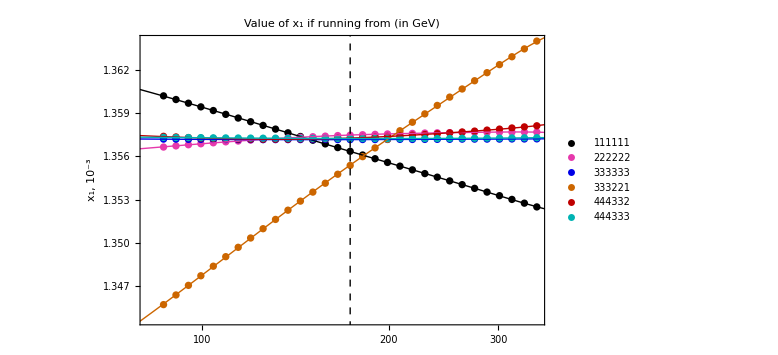

\begin{array}{ccccc}
 1.35635 & -3.1983 \text{pow}(-5) & 9.9376 \text{pow}(-8) & -4.1365 \text{pow}(-10) & 9.6709 \text{pow}(-13) \\
 1.35749 & 3.8461 \text{pow}(-6) & -3.7798 \text{pow}(-8) & 2.4732 \text{pow}(-10) & -6.85 \text{pow}(-13) \\
 1.35717 & 2.4223 \text{pow}(-7) & 2.9554 \text{pow}(-9) & -3.4754 \text{pow}(-11) & 1.1242 \text{pow}(-13) \\
 1.3554 & 7.5951 \text{pow}(-5) & -2.7701 \text{pow}(-7) & 1.2393 \text{pow}(-9) & -3.0172 \text{pow}(-12) \\
 1.35728 & 3.6037 \text{pow}(-6) & 2.8908 \text{pow}(-8) & -2.4186 \text{pow}(-10) & 6.9613 \text{pow}(-13) \\
 1.35725 & -1.8413 \text{pow}(-7) & 5.698 \text{pow}(-9) & -2.4707 \text{pow}(-11) & 5.128 \text{pow}(-14) \\
\end{array}

```mathematica
Show[
ListLogLinearPlot[Table[({#[[1]],1000 #[[2]]})&/@theorerr[[2+(i-1)32;;32+(i-1)32,{1,2}]],{i,1,6}],PlotStyle->loopColors,PlotLegends->{"111111","222222","333333","333221","444332","444333"},PlotRange->Full,Epilog->{{Dashed,InfiniteLine[{Log@173.22,0},{0,1}]}},FrameTicks -> {{Automatic,Automatic}, {Automatic, None}}, 
 PlotLabel ->  "Value of x_1 if running from  (in GeV)",  FrameLabel -> {"", "x_1, 10^-3"}, Frame -> True, 
 LabelStyle -> {FontSize -> 18, FontFamily -> "Times"},ImageSize->Large], Table[LogLinearPlot[LinearModelFit[({#[[1]],1000 #[[2]]})&/@theorerr[[2+(i-1)32;;32+(i-1)32,{1,2}]],{1,x,x^2,x^3,x^4},x][X],{X,50,400},PlotStyle->{loopColors[[i]],Thin}],{i,1,6}]
]
Export["figures/theorx1.pdf",%]
Table[(List@@LinearModelFit[({#[[1]],1000 #[[2]]})&/@theorerr[[2+(i-1)32;;32+(i-1)32,{1,2}]],{1,(x-173.22),(x-173.22)^2,(x-173.22)^3,(x-173.22)^4},x][X])/.X->(1+173.22),{i,1,6}]//Map[toPower,#,{2}]&//TableForm//TeXForm
```

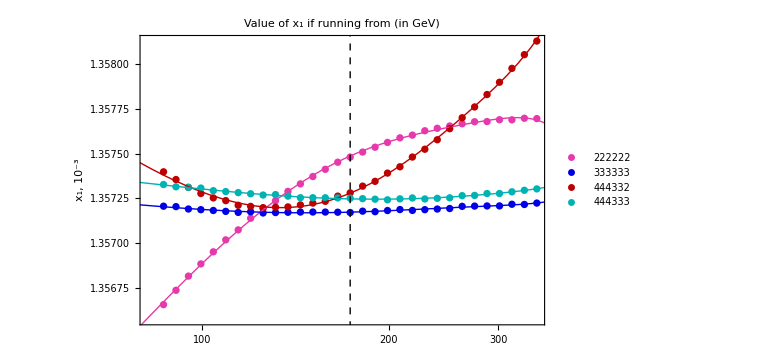

```mathematica
Show[
ListLogLinearPlot[Table[({#[[1]],1000 #[[2]]})&/@theorerr[[2+(i-1)32;;32+(i-1)32,{1,2}]],{i,{2,3,5,6}}],PlotStyle->loopColors[[{2,3,5,6}]],PlotLegends->{"222222","333333","444332","444333"},PlotRange->Full,Epilog->{Dashed,InfiniteLine[{Log@173.22,0},{0,1}]},FrameTicks -> {{Automatic,Automatic}, {Automatic, None}}, 
 PlotLabel ->  "Value of x_1 if running from  (in GeV)",  FrameLabel -> {"", "x_1, 10^-3"}, Frame -> True, 
 LabelStyle -> {FontSize -> 18, FontFamily -> "Times"},ImageSize->Large], Table[LogLinearPlot[LinearModelFit[({#[[1]],1000 #[[2]]})&/@theorerr[[2+(i-1)32;;32+(i-1)32,{1,2}]],{1,x,x^2,x^3,x^4},x][X],{X,50,400},PlotStyle->{loopColors[[i]],Thin}],{i,{2,3,5,6}}]
]
Export["figures/theorx1less.pdf",%]
```

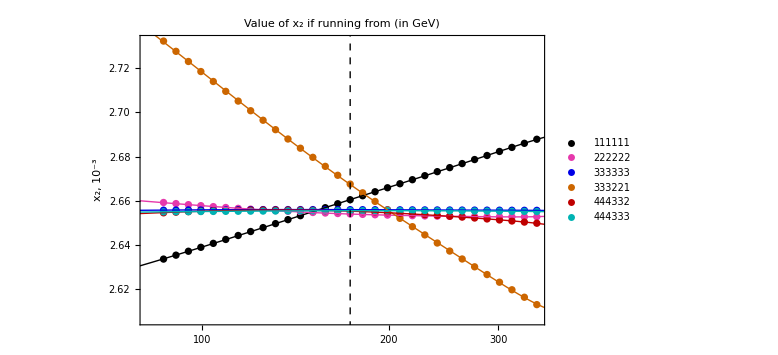

\begin{array}{ccccc}
 2.66056 & 2.2511 \text{pow}(-4) & -6.7877 \text{pow}(-7) & 2.8153 \text{pow}(-9) & -6.6747 \text{pow}(-12) \\
 2.65404 & -2.3944 \text{pow}(-5) & 2.3989 \text{pow}(-7) & -1.5748 \text{pow}(-9) & 4.4016 \text{pow}(-12) \\
 2.65603 & -1.9433 \text{pow}(-6) & -2.0162 \text{pow}(-8) & 2.7612 \text{pow}(-10) & -9.1927 \text{pow}(-13) \\
 2.66741 & -4.9284 \text{pow}(-4) & 1.9455 \text{pow}(-6) & -9.1526 \text{pow}(-9) & 2.2713 \text{pow}(-11) \\
 2.65534 & -2.31 \text{pow}(-5) & -1.8363 \text{pow}(-7) & 1.5559 \text{pow}(-9) & -4.5326 \text{pow}(-12) \\
 2.65555 & 1.3069 \text{pow}(-6) & -3.7712 \text{pow}(-8) & 1.5163 \text{pow}(-10) & -2.8519 \text{pow}(-13) \\
\end{array}

```mathematica
Show[
ListLogLinearPlot[Table[({#[[1]],1000 #[[2]]})&/@theorerr[[2+(i-1)32;;32+(i-1)32,{1,3}]],{i,1,6}],PlotStyle->loopColors,PlotLegends->{"111111","222222","333333","333221","444332","444333"},PlotRange->Full,Epilog->{Dashed,InfiniteLine[{Log@173.22,0},{0,1}]},FrameTicks -> {{Automatic,Automatic}, {Automatic, None}}, 
 PlotLabel ->  "Value of x_2 if running from  (in GeV)",  FrameLabel -> {"", "x_2, 10^-3"}, Frame -> True, 
 LabelStyle -> {FontSize -> 18, FontFamily -> "Times"},ImageSize->Large], Table[LogLinearPlot[LinearModelFit[({#[[1]],1000 #[[2]]})&/@theorerr[[2+(i-1)32;;32+(i-1)32,{1,3}]],{1,x,x^2,x^3,x^4},x][X],{X,50,400},PlotStyle->{loopColors[[i]],Thin}],{i,1,6}]
]
Export["figures/theorx2.pdf",%]
Table[(List@@LinearModelFit[({#[[1]],1000 #[[2]]})&/@theorerr[[2+(i-1)32;;32+(i-1)32,{1,3}]],{1,(x-173.22),(x-173.22)^2,(x-173.22)^3,(x-173.22)^4},x][X])/.X->(1+173.22),{i,1,6}]//Map[toPower,#,{2}]&//TableForm//TeXForm
```

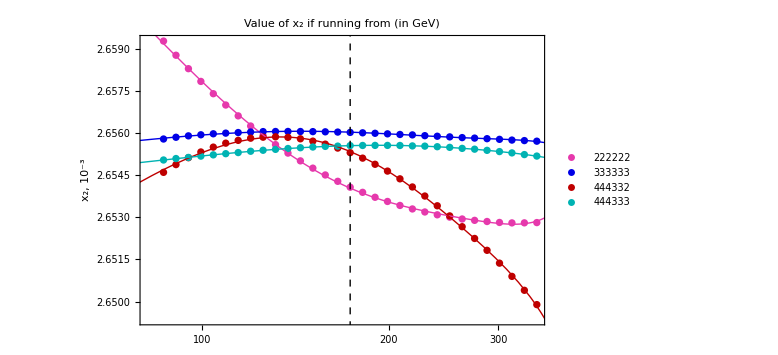

```mathematica
Show[
ListLogLinearPlot[Table[({#[[1]],1000 #[[2]]})&/@theorerr[[2+(i-1)32;;32+(i-1)32,{1,3}]],{i,{2,3,5,6}}],PlotStyle->loopColors[[{2,3,5,6}]],PlotLegends->{"222222","333333","444332","444333"},PlotRange->Full,Epilog->{Dashed,InfiniteLine[{Log@173.22,0},{0,1}]},FrameTicks -> {{Automatic,Automatic}, {Automatic, None}}, 
 PlotLabel ->  "Value of x_2 if running from  (in GeV)",  FrameLabel -> {"", "x_2, 10^-3"}, Frame -> True, 
 LabelStyle -> {FontSize -> 18, FontFamily -> "Times"},ImageSize->Large], Table[LogLinearPlot[LinearModelFit[({#[[1]],1000 #[[2]]})&/@theorerr[[2+(i-1)32;;32+(i-1)32,{1,3}]],{1,x,x^2,x^3,x^4},x][X],{X,50,400},PlotStyle->{loopColors[[i]],Thin}],{i,{2,3,5,6}}]
]
Export["figures/theorx2less.pdf",%]
```

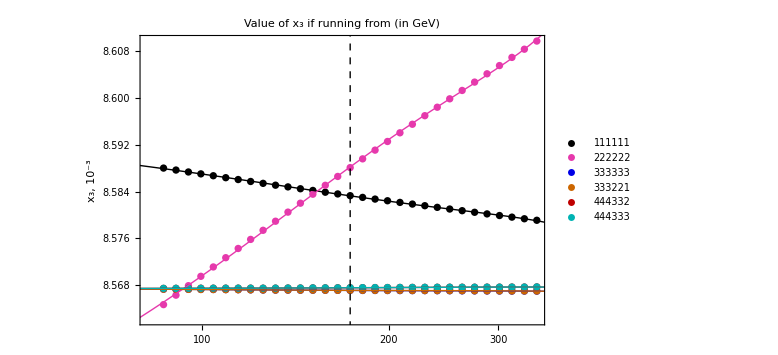

\begin{array}{ccccc}
 8.58327 & -3.8087 \text{pow}(-5) & 1.4677 \text{pow}(-7) & -3.9956 \text{pow}(-10) & \text{} \\
 8.58823 & 1.9376 \text{pow}(-4) & -6.9635 \text{pow}(-7) & 1.7709 \text{pow}(-9) & \text{} \\
 8.56708 & -1.0298 \text{pow}(-6) & 7.5889 \text{pow}(-9) & -9.1066 \text{pow}(-11) & 3.3401 \text{pow}(-13) \\
 8.56708 & -8.2853 \text{pow}(-7) & 6.7942 \text{pow}(-9) & -8.7061 \text{pow}(-11) & 3.0697 \text{pow}(-13) \\
 8.56753 & 1.4148 \text{pow}(-6) & -2.3953 \text{pow}(-9) & -4.8196 \text{pow}(-11) & 2.3268 \text{pow}(-13) \\
 8.56753 & 1.4239 \text{pow}(-6) & -2.6576 \text{pow}(-9) & -4.4962 \text{pow}(-11) & 2.2054 \text{pow}(-13) \\
\end{array}

```mathematica
Show[
ListLogLinearPlot[Table[({#[[1]],1000 #[[2]]})&/@theorerr[[2+(i-1)32;;32+(i-1)32,{1,4}]],{i,1,6}],PlotStyle->loopColors,PlotLegends->{"111111","222222","333333","333221","444332","444333"},PlotRange->Full,Epilog->{Dashed,InfiniteLine[{Log@173.22,0},{0,1}]},FrameTicks -> {{Automatic,Automatic}, {Automatic, None}}, 
 PlotLabel ->  "Value of x_3 if running from  (in GeV)",  FrameLabel -> {"", "x_3, 10^-3"}, Frame -> True, 
 LabelStyle -> {FontSize -> 18, FontFamily -> "Times"},ImageSize->Large], Table[LogLinearPlot[LinearModelFit[({#[[1]],1000 #[[2]]})&/@theorerr[[2+(i-1)32;;32+(i-1)32,{1,4}]],{1,x,x^2,x^3},x][X],{X,50,400},PlotStyle->{loopColors[[i]],Thin}],{i,1,6}]
]
Export["figures/theorx3.pdf",%]
Join[Table[(List@@LinearModelFit[({#[[1]],1000 #[[2]]})&/@theorerr[[2+(i-1)32;;32+(i-1)32,{1,4}]],{1,(x-173.22),(x-173.22)^2,(x-173.22)^3},x][X])/.X->(1+173.22),{i,1,2}]//Map[toPower,#,{2}]&,Table[(List@@LinearModelFit[({#[[1]],1000 #[[2]]})&/@theorerr[[2+(i-1)32;;32+(i-1)32,{1,4}]],{1,(x-173.22),(x-173.22)^2,(x-173.22)^3,(x-173.22)^4},x][X])/.X->(1+173.22),{i,3,6}]//Map[toPower,#,{2}]&]//TableForm//TeXForm
```

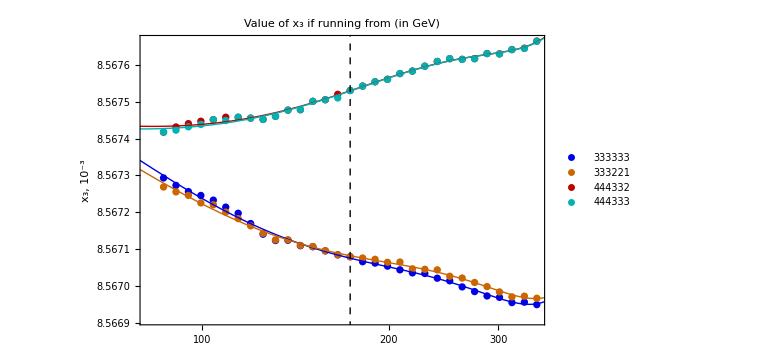

```mathematica
Show[
ListLogLinearPlot[Table[({#[[1]],1000 #[[2]]})&/@theorerr[[2+(i-1)32;;32+(i-1)32,{1,4}]],{i,3,6}],PlotStyle->loopColors[[3;;6]],PlotLegends->{"333333","333221","444332","444333"},PlotRange->Full,Epilog->{Dashed,InfiniteLine[{Log@173.22,0},{0,1}]},FrameTicks -> {{Automatic,Automatic}, {Automatic, None}}, 
 PlotLabel ->  "Value of x_3 if running from  (in GeV)",  FrameLabel -> {"", "x_3, 10^-3"}, Frame -> True, 
 LabelStyle -> {FontSize -> 18, FontFamily -> "Times"},ImageSize->Large], Table[LogLinearPlot[LinearModelFit[({#[[1]],1000 #[[2]]})&/@theorerr[[2+(i-1)32;;32+(i-1)32,{1,4}]],{1,x,x^2,x^3,x^4},x][X],{X,50,400},PlotStyle->{loopColors[[i]],Thin}],{i,3,6}]
]
Export["figures/theorx3less.pdf",%]
```

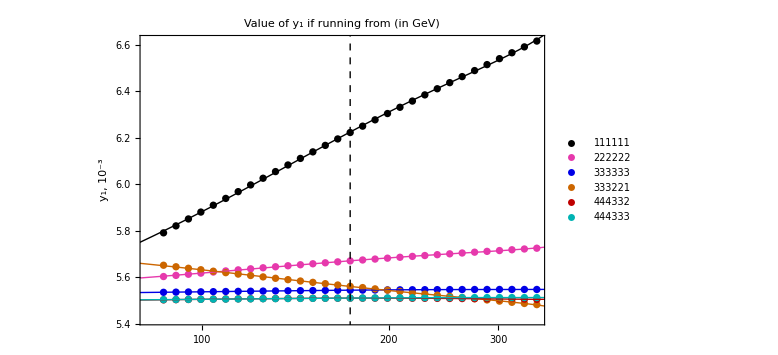

\begin{array}{ccccc}
 6.22375 & 3.5422 \text{pow}(-3) & -1.2971 \text{pow}(-5) & 3.3243 \text{pow}(-8) & \text{} \\
 5.66981 & 5.2285 \text{pow}(-4) & -2.2391 \text{pow}(-6) & 6.1501 \text{pow}(-9) & \text{} \\
 5.54344 & 5.6114 \text{pow}(-5) & -3.9517 \text{pow}(-7) & 1.6093 \text{pow}(-9) & -3.5287 \text{pow}(-12) \\
 5.55988 & -6.928 \text{pow}(-4) & 2.6551 \text{pow}(-6) & -1.3004 \text{pow}(-8) & 3.3082 \text{pow}(-11) \\
 5.5091 & 7.9529 \text{pow}(-6) & -5.2326 \text{pow}(-7) & 3.2169 \text{pow}(-9) & -8.5672 \text{pow}(-12) \\
 5.50944 & 4.297 \text{pow}(-5) & -2.9351 \text{pow}(-7) & 1.0501 \text{pow}(-9) & -2.0936 \text{pow}(-12) \\
\end{array}

```mathematica
Show[
ListLogLinearPlot[Table[({#[[1]],1000 #[[2]]})&/@theorerr[[2+(i-1)32;;32+(i-1)32,{1,5}]],{i,1,6}],PlotStyle->loopColors,PlotLegends->{"111111","222222","333333","333221","444332","444333"},PlotRange->Full,Epilog->{Dashed,InfiniteLine[{Log@173.22,0},{0,1}]},FrameTicks -> {{Automatic,Automatic}, {Automatic, None}}, 
 PlotLabel ->  "Value of y_1 if running from  (in GeV)",  FrameLabel -> {"", "y_1, 10^-3"}, Frame -> True, 
 LabelStyle -> {FontSize -> 18, FontFamily -> "Times"},ImageSize->Large], Table[LogLinearPlot[LinearModelFit[({#[[1]],1000 #[[2]]})&/@theorerr[[2+(i-1)32;;32+(i-1)32,{1,5}]],{1,x,x^2,x^3},x][X],{X,50,400},PlotStyle->{loopColors[[i]],Thin}],{i,1,6}]
]
Export["figures/theory1.pdf",%]
Join[Table[(List@@LinearModelFit[({#[[1]],1000 #[[2]]})&/@theorerr[[2+(i-1)32;;32+(i-1)32,{1,5}]],{1,(x-173.22),(x-173.22)^2,(x-173.22)^3},x][X])/.X->(1+173.22),{i,1,2}]//Map[toPower,#,{2}]&,Table[(List@@LinearModelFit[({#[[1]],1000 #[[2]]})&/@theorerr[[2+(i-1)32;;32+(i-1)32,{1,5}]],{1,(x-173.22),(x-173.22)^2,(x-173.22)^3,(x-173.22)^4},x][X])/.X->(1+173.22),{i,3,6}]//Map[toPower,#,{2}]&]//TableForm//TeXForm
```

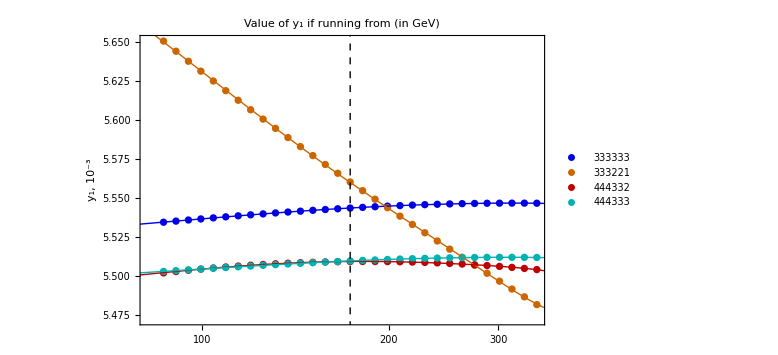

```mathematica
Show[
ListLogLinearPlot[Table[({#[[1]],1000 #[[2]]})&/@theorerr[[2+(i-1)32;;32+(i-1)32,{1,5}]],{i,3,6}],PlotStyle->loopColors[[3;;6]],PlotLegends->{"333333","333221","444332","444333"},PlotRange->Full,Epilog->{Dashed,InfiniteLine[{Log@173.22,0},{0,1}]},FrameTicks -> {{Automatic,Automatic}, {Automatic, None}}, 
 PlotLabel ->  "Value of y_1 if running from  (in GeV)",  FrameLabel -> {"", "y_1, 10^-3"}, Frame -> True, 
 LabelStyle -> {FontSize -> 18, FontFamily -> "Times"},ImageSize->Large], Table[LogLinearPlot[LinearModelFit[({#[[1]],1000 #[[2]]})&/@theorerr[[2+(i-1)32;;32+(i-1)32,{1,5}]],{1,x,x^2,x^3,x^4},x][X],{X,50,400},PlotStyle->{loopColors[[i]],Thin}],{i,3,6}]
]
Export["figures/theory1less.pdf",%]
```

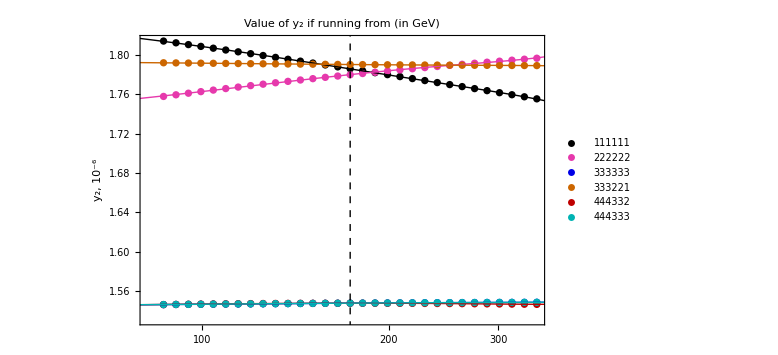

\begin{array}{ccccc}
 1.78569 & -2.5012 \text{pow}(-4) & 6.9784 \text{pow}(-7) & -1.5982 \text{pow}(-9) & \text{} \\
 1.77988 & 1.6738 \text{pow}(-4) & -7.6434 \text{pow}(-7) & 2.1146 \text{pow}(-9) & \text{} \\
 1.54771 & 9.889 \text{pow}(-6) & -5.3335 \text{pow}(-8) & 2.482 \text{pow}(-10) & -5.9172 \text{pow}(-13) \\
 1.79014 & -1.1604 \text{pow}(-5) & 6.2752 \text{pow}(-8) & -3.4336 \text{pow}(-10) & 9.1142 \text{pow}(-13) \\
 1.54767 & -3.802 \text{pow}(-7) & -1.0444 \text{pow}(-7) & 7.5687 \text{pow}(-10) & -2.1483 \text{pow}(-12) \\
 1.54774 & 9.5855 \text{pow}(-6) & -5.2343 \text{pow}(-8) & 2.4686 \text{pow}(-10) & -5.9154 \text{pow}(-13) \\
\end{array}

```mathematica
Show[
ListLogLinearPlot[Table[({#[[1]],10^(6) #[[2]]})&/@theorerr[[2+(i-1)32;;32+(i-1)32,{1,6}]],{i,1,6}],PlotStyle->loopColors,PlotLegends->{"111111","222222","333333","333221","444332","444333"},PlotRange->Full,Epilog->{Dashed,InfiniteLine[{Log@173.22,0},{0,1}]},FrameTicks -> {{Automatic,Automatic}, {Automatic, None}}, 
 PlotLabel ->  "Value of y_2 if running from  (in GeV)",  FrameLabel -> {"", "y_2, 10^-6"}, Frame -> True, 
 LabelStyle -> {FontSize -> 18, FontFamily -> "Times"},ImageSize->Large], Table[LogLinearPlot[LinearModelFit[({#[[1]],10^(6) #[[2]]})&/@theorerr[[2+(i-1)32;;32+(i-1)32,{1,6}]],{1,x,x^2,x^3},x][X],{X,50,400},PlotStyle->{loopColors[[i]],Thin}],{i,1,6}]
]
Export["figures/theory2.pdf",%]
Join[Table[(List@@LinearModelFit[({#[[1]],10^(6) #[[2]]})&/@theorerr[[2+(i-1)32;;32+(i-1)32,{1,6}]],{1,(x-173.22),(x-173.22)^2,(x-173.22)^3},x][X])/.X->(1+173.22),{i,1,2}]//Map[toPower,#,{2}]&,Table[(List@@LinearModelFit[({#[[1]],10^(6) #[[2]]})&/@theorerr[[2+(i-1)32;;32+(i-1)32,{1,6}]],{1,(x-173.22),(x-173.22)^2,(x-173.22)^3,(x-173.22)^4},x][X])/.X->(1+173.22),{i,3,6}]//Map[toPower,#,{2}]&]//TableForm//TeXForm
```

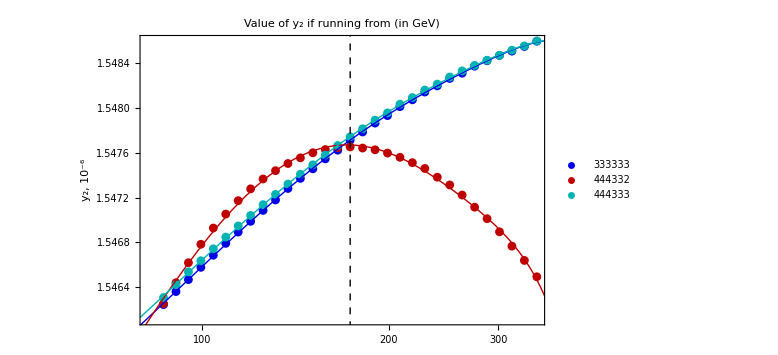

```mathematica
Show[
ListLogLinearPlot[Table[({#[[1]],10^(6) #[[2]]})&/@theorerr[[2+(i-1)32;;32+(i-1)32,{1,6}]],{i,{3,5,6}}],PlotStyle->loopColors[[{3,5,6}]],PlotLegends->{"333333","444332","444333"},PlotRange->Full,Epilog->{Dashed,InfiniteLine[{Log@173.22,0},{0,1}]},FrameTicks -> {{Automatic,Automatic}, {Automatic, None}}, 
 PlotLabel ->  "Value of y_2 if running from  (in GeV)",  FrameLabel -> {"", "y_2, 10^-6"}, Frame -> True, 
 LabelStyle -> {FontSize -> 18, FontFamily -> "Times"},ImageSize->Large], Table[LogLinearPlot[LinearModelFit[({#[[1]],10^(6) #[[2]]})&/@theorerr[[2+(i-1)32;;32+(i-1)32,{1,6}]],{1,x,x^2,x^3,x^4},x][X],{X,50,400},PlotStyle->{loopColors[[i]],Thin}],{i,{3,5,6}}]
]
Export["figures/theory2less.pdf",%]
```

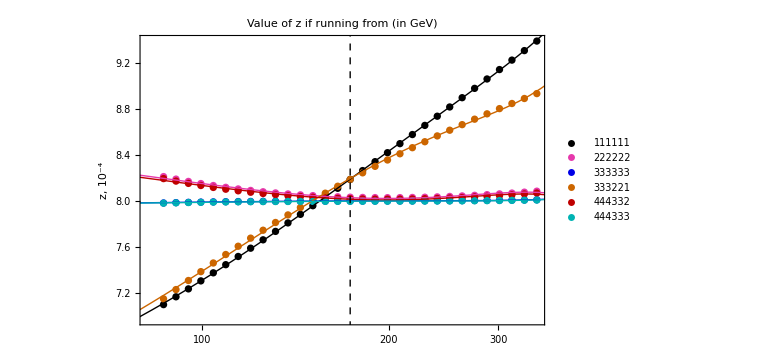

\begin{array}{ccccc}
 8.18994 & 9.7948 \text{pow}(-3) & -2.6217 \text{pow}(-5) & 5.8188 \text{pow}(-8) & \text{} \\
 8.03029 & -3.2276 \text{pow}(-4) & 1.0866 \text{pow}(-5) & -8.2066 \text{pow}(-8) & 2.3752 \text{pow}(-10) \\
 7.99916 & 1.6464 \text{pow}(-5) & -5.3254 \text{pow}(-7) & 1.2129 \text{pow}(-8) & -4.4503 \text{pow}(-11) \\
 8.19535 & 7.6885 \text{pow}(-3) & -3.7693 \text{pow}(-5) & 1.0786 \text{pow}(-7) & \text{} \\
 8.01672 & -2.9906 \text{pow}(-4) & 1.0575 \text{pow}(-5) & -8.2142 \text{pow}(-8) & 2.4012 \text{pow}(-10) \\
 7.99694 & 1.4964 \text{pow}(-5) & -5.069 \text{pow}(-7) & 1.187 \text{pow}(-8) & -4.3685 \text{pow}(-11) \\
\end{array}

```mathematica
Show[
ListLogLinearPlot[Table[({#[[1]],10^(4) #[[2]]})&/@theorerr[[2+(i-1)32;;32+(i-1)32,{1,7}]],{i,1,6}],PlotStyle->loopColors,PlotLegends->{"111111","222222","333333","333221","444332","444333"},PlotRange->Full,Epilog->{Dashed,InfiniteLine[{Log@173.22,0},{0,1}]},FrameTicks -> {{Automatic,Automatic}, {Automatic, None}}, 
 PlotLabel ->  "Value of z if running from  (in GeV)",  FrameLabel -> {"", "z, 10^-4"}, Frame -> True, 
 LabelStyle -> {FontSize -> 18, FontFamily -> "Times"},ImageSize->Large], Table[LogLinearPlot[LinearModelFit[({#[[1]],10^(4) #[[2]]})&/@theorerr[[2+(i-1)32;;32+(i-1)32,{1,7}]],{1,x,x^2,x^3},x][X],{X,50,400},PlotStyle->{loopColors[[i]],Thin}],{i,1,6}]
]
Export["figures/theorz.pdf",%]
Join[Table[(List@@LinearModelFit[({#[[1]],10^(4) #[[2]]})&/@theorerr[[2+(i-1)32;;32+(i-1)32,{1,7}]],{1,(x-173.22),(x-173.22)^2,(x-173.22)^3},x][X])/.X->(1+173.22),{i,{1,4}}]//Map[toPower,#,{2}]&,Table[(List@@LinearModelFit[({#[[1]],10^(4) #[[2]]})&/@theorerr[[2+(i-1)32;;32+(i-1)32,{1,7}]],{1,(x-173.22),(x-173.22)^2,(x-173.22)^3,(x-173.22)^4},x][X])/.X->(1+173.22),{i,{2,3,5,6}}]//Map[toPower,#,{2}]&][[{1,3,4,2,5,6}]]//TableForm//TeXForm
```

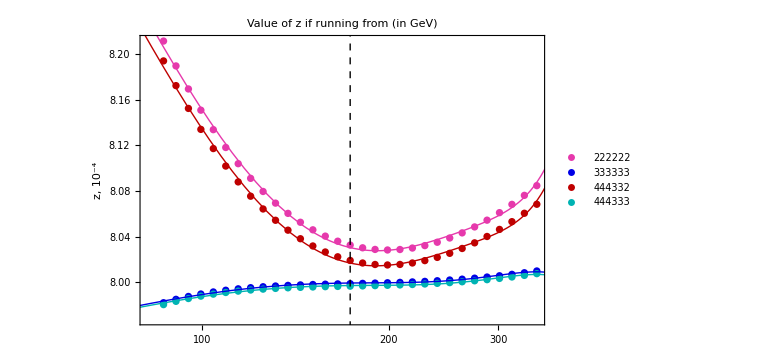

```mathematica
Show[
ListLogLinearPlot[Table[({#[[1]],10^(4) #[[2]]})&/@theorerr[[2+(i-1)32;;32+(i-1)32,{1,7}]],{i,{2,3,5,6}}],PlotStyle->loopColors[[{2,3,5,6}]],PlotLegends->{"222222","333333","444332","444333"},PlotRange->Full,Epilog->{Dashed,InfiniteLine[{Log@173.22,0},{0,1}]},FrameTicks -> {{Automatic,Automatic}, {Automatic, None}}, 
 PlotLabel ->  "Value of z if running from  (in GeV)",  FrameLabel -> {"", "z, 10^-4"}, Frame -> True, 
 LabelStyle -> {FontSize -> 18, FontFamily -> "Times"},ImageSize->Large], Table[LogLinearPlot[LinearModelFit[({#[[1]],10^(4) #[[2]]})&/@theorerr[[2+(i-1)32;;32+(i-1)32,{1,7}]],{1,x,x^2,x^3,x^4},x][X],{X,50,400},PlotStyle->{loopColors[[i]],Thin}],{i,{2,3,5,6}}]
]
Export["figures/theorzless.pdf",%]
```

```mathematica
toPower[n_]:=If[NumberQ[n],
If[Abs@Log10[n]>=3,
n/10^Floor@Log10[Abs@n]*pow[Floor@Log10[Abs@n]],
n
],
n
];
```

```mathematica
theorerr//Map[toPower,#,{2}]&//TableForm//TeXForm
```

\begin{array}{ccccccc}
 \text{(1,1,1;1,1;1)} & \text{} & \text{} & \text{} & \text{} & \text{} & \text{} \\
 86.61 & 0.00136021 & 0.00263365 & 0.00858803 & 0.00579004 & 1.81395 \text{pow}(-6) & 7.09581 \text{pow}(-4) \\
 115.48 & 0.00135861 & 0.00264474 & 0.00858598 & 0.00597376 & 1.80259 \text{pow}(-6) & 7.53173 \text{pow}(-4) \\
 173.22 & 0.00135636 & 0.00266051 & 0.0085833 & 0.0062215 & 1.78578 \text{pow}(-6) & 8.18679 \text{pow}(-4) \\
 259.83 & 0.00135411 & 0.00267646 & 0.0085808 & 0.0064562 & 1.76816 \text{pow}(-6) & 8.88131 \text{pow}(-4) \\
 346.44 & 0.0013525 & 0.00268788 & 0.00857909 & 0.00661491 & 1.75525 \text{pow}(-6) & 9.39321 \text{pow}(-4) \\
 \text{(2,2,2;2,2;2)} & \text{} & \text{} & \text{} & \text{} & \text{} & \text{} \\
 86.61 & 0.00135666 & 0.00265928 & 0.00856463 & 0.00560209 & 1.7577 \text{pow}(-6) & 8.21176 \text{pow}(-4) \\
 115.48 & 0.00135708 & 0.00265652 & 0.00857461 & 0.00563183 & 1.76755 \text{pow}(-6) & 8.10098 \text{pow}(-4) \\
 173.22 & 0.00135748 & 0.00265407 & 0.00858811 & 0.00566935 & 1.77972 \text{pow}(-6) & 8.0325 \text{pow}(-4) \\
 259.83 & 0.00135767 & 0.00265296 & 0.008601 & 0.00570258 & 1.79011 \text{pow}(-6) & 8.04214 \text{pow}(-4) \\
 346.44 & 0.00135769 & 0.0026528 & 0.00860979 & 0.00572398 & 1.79652 \text{pow}(-6) & 8.08471 \text{pow}(-4) \\
 \text{(3,3,3;3,3;3)} & \text{} & \text{} & \text{} & \text{} & \text{} & \text{} \\
 86.61 & 0.00135721 & 0.00265578 & 0.00856729 & 0.00553432 & 1.54625 \text{pow}(-6) & 7.98185 \text{pow}(-4) \\
 115.48 & 0.00135717 & 0.00265603 & 0.00856718 & 0.00553857 & 1.54691 \text{pow}(-6) & 7.99428 \text{pow}(-4) \\
 173.22 & 0.00135717 & 0.00265602 & 0.00856708 & 0.00554341 & 1.54771 \text{pow}(-6) & 7.99861 \text{pow}(-4) \\
 259.83 & 0.0013572 & 0.00265584 & 0.00856701 & 0.0055462 & 1.5483 \text{pow}(-6) & 8.00238 \text{pow}(-4) \\
 346.44 & 0.00135722 & 0.00265571 & 0.00856694 & 0.00554652 & 1.54858 \text{pow}(-6) & 8.00973 \text{pow}(-4) \\
 \text{(3,3,3;2,2;1)} & \text{} & \text{} & \text{} & \text{} & \text{} & \text{} \\
 86.61 & 0.00134572 & 0.00273232 & 0.00856727 & 0.00565071 & 1.7919 \text{pow}(-6) & 7.14617 \text{pow}(-4) \\
 115.48 & 0.00134985 & 0.00270416 & 0.00856718 & 0.00561129 & 1.79109 \text{pow}(-6) & 7.62073 \text{pow}(-4) \\
 173.22 & 0.00135538 & 0.00266759 & 0.00856708 & 0.00556014 & 1.79015 \text{pow}(-6) & 8.18679 \text{pow}(-4) \\
 259.83 & 0.00136055 & 0.00263451 & 0.00856702 & 0.00551298 & 1.78943 \text{pow}(-6) & 8.65381 \text{pow}(-4) \\
 346.44 & 0.001364 & 0.00261306 & 0.00856697 & 0.00548136 & 1.78904 \text{pow}(-6) & 8.93528 \text{pow}(-4) \\
 \text{(4,4,4;3,3;2)} & \text{} & \text{} & \text{} & \text{} & \text{} & \text{} \\
 86.61 & 0.00135739 & 0.00265461 & 0.00856742 & 0.00550174 & 1.54626 \text{pow}(-6) & 8.19432 \text{pow}(-4) \\
 115.48 & 0.00135721 & 0.00265576 & 0.00856746 & 0.00550627 & 1.54719 \text{pow}(-6) & 8.08504 \text{pow}(-4) \\
 173.22 & 0.00135728 & 0.0026553 & 0.00856753 & 0.00550903 & 1.54765 \text{pow}(-6) & 8.01898 \text{pow}(-4) \\
 259.83 & 0.00135768 & 0.00265275 & 0.00856762 & 0.00550754 & 1.54724 \text{pow}(-6) & 8.02849 \text{pow}(-4) \\
 346.44 & 0.00135813 & 0.00264988 & 0.00856765 & 0.00550389 & 1.5465 \text{pow}(-6) & 8.06837 \text{pow}(-4) \\
 \text{(4,4,4;3,3;3)} & \text{} & \text{} & \text{} & \text{} & \text{} & \text{} \\
 86.61 & 0.00135733 & 0.00265504 & 0.00856741 & 0.0055027 & 1.54631 \text{pow}(-6) & 7.98019 \text{pow}(-4) \\
 115.48 & 0.00135728 & 0.00265531 & 0.00856746 & 0.00550577 & 1.54697 \text{pow}(-6) & 7.99229 \text{pow}(-4) \\
 173.22 & 0.00135725 & 0.00265555 & 0.00856753 & 0.00550943 & 1.54774 \text{pow}(-6) & 7.9964 \text{pow}(-4) \\
 259.83 & 0.00135726 & 0.00265546 & 0.00856762 & 0.00551154 & 1.54831 \text{pow}(-6) & 8.00008 \text{pow}(-4) \\
 346.44 & 0.0013573 & 0.00265517 & 0.00856765 & 0.00551167 & 1.54858 \text{pow}(-6) & 8.0074 \text{pow}(-4) \\
\end{array}

```mathematica
toPower[n_]:=If[NumberQ[n],
If[Abs@Log10[n]>=2,
N@Round[n/10^Floor@Log10[Abs@n]*10000]/10000*pow[Floor@Log10[Abs@n]],
N@Round[n * 100000] / 100000
],
n
];
```

```mathematica
Table[{Join[{"","max th"},Table[Max[theorerr[[2+(i-1)32;;32+(i-1)32,j]]],{i,1,3}]],Join[{"multirow","min th"},Table[Min[theorerr[[2+(i-1)32;;32+(i-1)32,j]]],{i,1,3}]]}//Map[toPower,#,{2}]&,{j,2,7}]//Flatten[#,1]&//TeXForm
```

\left(
\begin{array}{ccccc}
 \text{} & \text{max th} & 1.3602 \text{pow}(-3) & 1.3577 \text{pow}(-3) & 1.3572 \text{pow}(-3) \\
 \text{multirow} & \text{min th} & 1.3525 \text{pow}(-3) & 1.3567 \text{pow}(-3) & 1.3572 \text{pow}(-3) \\
 \text{} & \text{max th} & 2.6879 \text{pow}(-3) & 2.6593 \text{pow}(-3) & 2.6561 \text{pow}(-3) \\
 \text{multirow} & \text{min th} & 2.6337 \text{pow}(-3) & 2.6528 \text{pow}(-3) & 2.6557 \text{pow}(-3) \\
 \text{} & \text{max th} & 8.588 \text{pow}(-3) & 8.6098 \text{pow}(-3) & 8.5673 \text{pow}(-3) \\
 \text{multirow} & \text{min th} & 8.5791 \text{pow}(-3) & 8.5646 \text{pow}(-3) & 8.567 \text{pow}(-3) \\
 \text{} & \text{max th} & 6.6149 \text{pow}(-3) & 5.724 \text{pow}(-3) & 5.5466 \text{pow}(-3) \\
 \text{multirow} & \text{min th} & 5.7901 \text{pow}(-3) & 5.6021 \text{pow}(-3) & 5.5343 \text{pow}(-3) \\
 \text{} & \text{max th} & 1.814 \text{pow}(-6) & 1.7965 \text{pow}(-6) & 1.5486 \text{pow}(-6) \\
 \text{multirow} & \text{min th} & 1.7553 \text{pow}(-6) & 1.7577 \text{pow}(-6) & 1.5462 \text{pow}(-6) \\
 \text{} & \text{max th} & 9.3931 \text{pow}(-4) & 8.2117 \text{pow}(-4) & 8.0097 \text{pow}(-4) \\
 \text{multirow} & \text{min th} & 7.0959 \text{pow}(-4) & 8.0282 \text{pow}(-4) & 7.9818 \text{pow}(-4) \\
\end{array}
\right)

```mathematica
Table[{Join[{"","max th"},Table[Max[theorerr[[2+(i-1)32;;32+(i-1)32,j]]],{i,4,6}]],Join[{"multirow","min th"},Table[Min[theorerr[[2+(i-1)32;;32+(i-1)32,j]]],{i,4,6}]]}//Map[toPower,#,{2}]&,{j,2,7}]//Flatten[#,1]&//TeXForm
```

\left(
\begin{array}{ccccc}
 \text{} & \text{max th} & 1.364 \text{pow}(-3) & 1.3581 \text{pow}(-3) & 1.3573 \text{pow}(-3) \\
 \text{multirow} & \text{min th} & 1.3457 \text{pow}(-3) & 1.3572 \text{pow}(-3) & 1.3572 \text{pow}(-3) \\
 \text{} & \text{max th} & 2.7323 \text{pow}(-3) & 2.6559 \text{pow}(-3) & 2.6556 \text{pow}(-3) \\
 \text{multirow} & \text{min th} & 2.6131 \text{pow}(-3) & 2.6499 \text{pow}(-3) & 2.655 \text{pow}(-3) \\
 \text{} & \text{max th} & 8.5673 \text{pow}(-3) & 8.5677 \text{pow}(-3) & 8.5677 \text{pow}(-3) \\
 \text{multirow} & \text{min th} & 8.567 \text{pow}(-3) & 8.5674 \text{pow}(-3) & 8.5674 \text{pow}(-3) \\
 \text{} & \text{max th} & 5.6507 \text{pow}(-3) & 5.5091 \text{pow}(-3) & 5.5118 \text{pow}(-3) \\
 \text{multirow} & \text{min th} & 5.4814 \text{pow}(-3) & 5.5017 \text{pow}(-3) & 5.5027 \text{pow}(-3) \\
 \text{} & \text{max th} & 1.7919 \text{pow}(-6) & 1.5476 \text{pow}(-6) & 1.5486 \text{pow}(-6) \\
 \text{multirow} & \text{min th} & 1.789 \text{pow}(-6) & 1.5463 \text{pow}(-6) & 1.5463 \text{pow}(-6) \\
 \text{} & \text{max th} & 8.9352 \text{pow}(-4) & 8.1943 \text{pow}(-4) & 8.0074 \text{pow}(-4) \\
 \text{multirow} & \text{min th} & 7.1463 \text{pow}(-4) & 8.015 \text{pow}(-4) & 7.9802 \text{pow}(-4) \\
\end{array}
\right)

```mathematica
theorsols[1,1,1,1,1,1]=Table[NDSolve[
{x1'[t]==((x1dot[1,1,1,1,1,1])/.{x1->x1[t],x2->x2[t],x3->x3[t],y1->y1[t],y2->y2[t],z->z[t]}),x2'[t]==((x2dot[1,1,1,1,1,1])/.{x1->x1[t],x2->x2[t],x3->x3[t],y1->y1[t],y2->y2[t],z->z[t]}),x3'[t]==((x3dot[1,1,1,1,1,1])/.{x1->x1[t],x2->x2[t],x3->x3[t],y1->y1[t],y2->y2[t],z->z[t]}),y1'[t]==((y1dot[1,1,1,1,1,1])/.{x1->x1[t],x2->x2[t],x3->x3[t],y1->y1[t],y2->y2[t],z->z[t]}),y2'[t]==((y2dot[1,1,1,1,1,1])/.{x1->x1[t],x2->x2[t],x3->x3[t],y1->y1[t],y2->y2[t],z->z[t]}),z'[t]==((zdot[1,1,1,1,1,1])/.{x1->x1[t],x2->x2[t],x3->x3[t],y1->y1[t],y2->y2[t],z->z[t]}), 
x1[0]==theorerr[[i,2]],x2[0]==theorerr[[i,3]],x3[0]==theorerr[[i,4]],y1[0]==theorerr[[i,5]],y2[0]==theorerr[[i,6]],z[0]==theorerr[[i,7]]}
,{x1[t],x2[t],x3[t],y1[t],y2[t],z[t]},
{t,0,150}][[1,6]]
,{i,2,32}];
theorsols[2,2,2,2,2,2]=Table[NDSolve[
{x1'[t]==((x1dot[2,2,2,2,2,2])/.{x1->x1[t],x2->x2[t],x3->x3[t],y1->y1[t],y2->y2[t],z->z[t]}),x2'[t]==((x2dot[2,2,2,2,2,2])/.{x1->x1[t],x2->x2[t],x3->x3[t],y1->y1[t],y2->y2[t],z->z[t]}),x3'[t]==((x3dot[2,2,2,2,2,2])/.{x1->x1[t],x2->x2[t],x3->x3[t],y1->y1[t],y2->y2[t],z->z[t]}),y1'[t]==((y1dot[2,2,2,2,2,2])/.{x1->x1[t],x2->x2[t],x3->x3[t],y1->y1[t],y2->y2[t],z->z[t]}),y2'[t]==((y2dot[2,2,2,2,2,2])/.{x1->x1[t],x2->x2[t],x3->x3[t],y1->y1[t],y2->y2[t],z->z[t]}),z'[t]==((zdot[2,2,2,2,2,2])/.{x1->x1[t],x2->x2[t],x3->x3[t],y1->y1[t],y2->y2[t],z->z[t]}), 
x1[0]==theorerr[[i,2]],x2[0]==theorerr[[i,3]],x3[0]==theorerr[[i,4]],y1[0]==theorerr[[i,5]],y2[0]==theorerr[[i,6]],z[0]==theorerr[[i,7]]}
,{x1[t],x2[t],x3[t],y1[t],y2[t],z[t]},
{t,0,150}][[1,6]]
,{i,34,64}];
theorsols[3,3,3,3,3,3]=Table[NDSolve[
{x1'[t]==((x1dot[3,3,3,3,3,3])/.{x1->x1[t],x2->x2[t],x3->x3[t],y1->y1[t],y2->y2[t],z->z[t]}),x2'[t]==((x2dot[3,3,3,3,3,3])/.{x1->x1[t],x2->x2[t],x3->x3[t],y1->y1[t],y2->y2[t],z->z[t]}),x3'[t]==((x3dot[3,3,3,3,3,3])/.{x1->x1[t],x2->x2[t],x3->x3[t],y1->y1[t],y2->y2[t],z->z[t]}),y1'[t]==((y1dot[3,3,3,3,3,3])/.{x1->x1[t],x2->x2[t],x3->x3[t],y1->y1[t],y2->y2[t],z->z[t]}),y2'[t]==((y2dot[3,3,3,3,3,3])/.{x1->x1[t],x2->x2[t],x3->x3[t],y1->y1[t],y2->y2[t],z->z[t]}),z'[t]==((zdot[3,3,3,3,3,3])/.{x1->x1[t],x2->x2[t],x3->x3[t],y1->y1[t],y2->y2[t],z->z[t]}), 
x1[0]==theorerr[[i,2]],x2[0]==theorerr[[i,3]],x3[0]==theorerr[[i,4]],y1[0]==theorerr[[i,5]],y2[0]==theorerr[[i,6]],z[0]==theorerr[[i,7]]}
,{x1[t],x2[t],x3[t],y1[t],y2[t],z[t]},
{t,0,150}][[1,6]]
,{i,66,96}];
theorsols[3,3,3,2,2,1]=Table[NDSolve[
{x1'[t]==((x1dot[3,3,3,2,2,1])/.{x1->x1[t],x2->x2[t],x3->x3[t],y1->y1[t],y2->y2[t],z->z[t]}),x2'[t]==((x2dot[3,3,3,2,2,1])/.{x1->x1[t],x2->x2[t],x3->x3[t],y1->y1[t],y2->y2[t],z->z[t]}),x3'[t]==((x3dot[3,3,3,2,2,1])/.{x1->x1[t],x2->x2[t],x3->x3[t],y1->y1[t],y2->y2[t],z->z[t]}),y1'[t]==((y1dot[3,3,3,2,2,1])/.{x1->x1[t],x2->x2[t],x3->x3[t],y1->y1[t],y2->y2[t],z->z[t]}),y2'[t]==((y2dot[3,3,3,2,2,1])/.{x1->x1[t],x2->x2[t],x3->x3[t],y1->y1[t],y2->y2[t],z->z[t]}),z'[t]==((zdot[3,3,3,2,2,1])/.{x1->x1[t],x2->x2[t],x3->x3[t],y1->y1[t],y2->y2[t],z->z[t]}), 
x1[0]==theorerr[[i,2]],x2[0]==theorerr[[i,3]],x3[0]==theorerr[[i,4]],y1[0]==theorerr[[i,5]],y2[0]==theorerr[[i,6]],z[0]==theorerr[[i,7]]}
,{x1[t],x2[t],x3[t],y1[t],y2[t],z[t]},
{t,0,150}][[1,6]]
,{i,98,128}];
theorsols[4,4,4,3,3,2]=Table[NDSolve[
{x1'[t]==((x1dot[4,4,4,3,3,2])/.{x1->x1[t],x2->x2[t],x3->x3[t],y1->y1[t],y2->y2[t],z->z[t]}),x2'[t]==((x2dot[4,4,4,3,3,2])/.{x1->x1[t],x2->x2[t],x3->x3[t],y1->y1[t],y2->y2[t],z->z[t]}),x3'[t]==((x3dot[4,4,4,3,3,2])/.{x1->x1[t],x2->x2[t],x3->x3[t],y1->y1[t],y2->y2[t],z->z[t]}),y1'[t]==((y1dot[4,4,4,3,3,2])/.{x1->x1[t],x2->x2[t],x3->x3[t],y1->y1[t],y2->y2[t],z->z[t]}),y2'[t]==((y2dot[4,4,4,3,3,2])/.{x1->x1[t],x2->x2[t],x3->x3[t],y1->y1[t],y2->y2[t],z->z[t]}),z'[t]==((zdot[4,4,4,3,3,2])/.{x1->x1[t],x2->x2[t],x3->x3[t],y1->y1[t],y2->y2[t],z->z[t]}), 
x1[0]==theorerr[[i,2]],x2[0]==theorerr[[i,3]],x3[0]==theorerr[[i,4]],y1[0]==theorerr[[i,5]],y2[0]==theorerr[[i,6]],z[0]==theorerr[[i,7]]}
,{x1[t],x2[t],x3[t],y1[t],y2[t],z[t]},
{t,0,150}][[1,6]]
,{i,130,160}];
theorsols[4,4,4,3,3,3]=Table[NDSolve[
{x1'[t]==((x1dot[4,4,4,3,3,3])/.{x1->x1[t],x2->x2[t],x3->x3[t],y1->y1[t],y2->y2[t],z->z[t]}),x2'[t]==((x2dot[4,4,4,3,3,3])/.{x1->x1[t],x2->x2[t],x3->x3[t],y1->y1[t],y2->y2[t],z->z[t]}),x3'[t]==((x3dot[4,4,4,3,3,3])/.{x1->x1[t],x2->x2[t],x3->x3[t],y1->y1[t],y2->y2[t],z->z[t]}),y1'[t]==((y1dot[4,4,4,3,3,3])/.{x1->x1[t],x2->x2[t],x3->x3[t],y1->y1[t],y2->y2[t],z->z[t]}),y2'[t]==((y2dot[4,4,4,3,3,3])/.{x1->x1[t],x2->x2[t],x3->x3[t],y1->y1[t],y2->y2[t],z->z[t]}),z'[t]==((zdot[4,4,4,3,3,3])/.{x1->x1[t],x2->x2[t],x3->x3[t],y1->y1[t],y2->y2[t],z->z[t]}), 
x1[0]==theorerr[[i,2]],x2[0]==theorerr[[i,3]],x3[0]==theorerr[[i,4]],y1[0]==theorerr[[i,5]],y2[0]==theorerr[[i,6]],z[0]==theorerr[[i,7]]}
,{x1[t],x2[t],x3[t],y1[t],y2[t],z[t]},
{t,0,150}][[1,6]]
,{i,162,192}];
```

```mathematica
FindRoot[theorsols[1,1,1,1,1,1][[1,2]],{t,11}][[1,2]]
```

14.994

```mathematica
{minRoot[1,1,1,1,1,1],maxRoot[1,1,1,1,1,1]}=MinMax@Table[FindRoot[theorsols[1,1,1,1,1,1][[i,2]],{t,11}][[1,2]],{i,1,Length@theorsols[1,1,1,1,1,1]}];
{minRoot[2,2,2,2,2,2],maxRoot[2,2,2,2,2,2]}=MinMax@Table[FindRoot[theorsols[2,2,2,2,2,2][[i,2]],{t,11}][[1,2]],{i,1,Length@theorsols[2,2,2,2,2,2]}];
{minRoot[3,3,3,3,3,3],maxRoot[3,3,3,3,3,3]}=MinMax@Table[FindRoot[theorsols[3,3,3,3,3,3][[i,2]],{t,11}][[1,2]],{i,1,Length@theorsols[3,3,3,3,3,3]}];
{minRoot[3,3,3,2,2,1],maxRoot[3,3,3,2,2,1]}=MinMax@Table[FindRoot[theorsols[3,3,3,2,2,1][[i,2]],{t,11}][[1,2]],{i,1,Length@theorsols[3,3,3,2,2,1]}];
{minRoot[4,4,4,3,3,2],maxRoot[4,4,4,3,3,2]}=MinMax@Table[FindRoot[theorsols[4,4,4,3,3,2][[i,2]],{t,11}][[1,2]],{i,1,Length@theorsols[4,4,4,3,3,2]}];
{minRoot[4,4,4,3,3,3],maxRoot[4,4,4,3,3,3]}=MinMax@Table[FindRoot[theorsols[4,4,4,3,3,3][[i,2]],{t,11}][[1,2]],{i,1,Length@theorsols[4,4,4,3,3,3]}];

{minMin[1,1,1,1,1,1],maxMin[1,1,1,1,1,1]}=MinMax@Table[FindMinimum[{theorsols[1,1,1,1,1,1][[i,2]],10<=t<=80},{t,60}][[1]],{i,1,Length@theorsols[1,1,1,1,1,1]}];
{minMin[2,2,2,2,2,2],maxMin[2,2,2,2,2,2]}=MinMax@Table[FindMinimum[{theorsols[2,2,2,2,2,2][[i,2]],10<=t<=80},{t,60}][[1]],{i,1,Length@theorsols[2,2,2,2,2,2]}];
{minMin[3,3,3,3,3,3],maxMin[3,3,3,3,3,3]}=MinMax@Table[FindMinimum[{theorsols[3,3,3,3,3,3][[i,2]],10<=t<=80},{t,60}][[1]],{i,1,Length@theorsols[3,3,3,3,3,3]}];
{minMin[3,3,3,2,2,1],maxMin[3,3,3,2,2,1]}=MinMax@Table[FindMinimum[{theorsols[3,3,3,2,2,1][[i,2]],10<=t<=80},{t,60}][[1]],{i,1,Length@theorsols[3,3,3,2,2,1]}];
{minMin[4,4,4,3,3,2],maxMin[4,4,4,3,3,2]}=MinMax@Table[FindMinimum[{theorsols[4,4,4,3,3,2][[i,2]],10<=t<=80},{t,60}][[1]],{i,1,Length@theorsols[4,4,4,3,3,2]}];
{minMin[4,4,4,3,3,3],maxMin[4,4,4,3,3,3]}=MinMax@Table[FindMinimum[{theorsols[4,4,4,3,3,3][[i,2]],10<=t<=80},{t,60}][[1]],{i,1,Length@theorsols[4,4,4,3,3,3]}];

{minTofMin[1,1,1,1,1,1],maxTofMin[1,1,1,1,1,1]}=MinMax@Table[FindMinimum[{theorsols[1,1,1,1,1,1][[i,2]],10<=t<=80},{t,60}][[2,1,2]],{i,1,Length@theorsols[1,1,1,1,1,1]}];
{minTofMin[2,2,2,2,2,2],maxTofMin[2,2,2,2,2,2]}=MinMax@Table[FindMinimum[{theorsols[2,2,2,2,2,2][[i,2]],10<=t<=80},{t,60}][[2,1,2]],{i,1,Length@theorsols[2,2,2,2,2,2]}];
{minTofMin[3,3,3,3,3,3],maxTofMin[3,3,3,3,3,3]}=MinMax@Table[FindMinimum[{theorsols[3,3,3,3,3,3][[i,2]],10<=t<=80},{t,60}][[2,1,2]],{i,1,Length@theorsols[3,3,3,3,3,3]}];
{minTofMin[3,3,3,2,2,1],maxTofMin[3,3,3,2,2,1]}=MinMax@Table[FindMinimum[{theorsols[3,3,3,2,2,1][[i,2]],10<=t<=80},{t,60}][[2,1,2]],{i,1,Length@theorsols[3,3,3,2,2,1]}];
{minTofMin[4,4,4,3,3,2],maxTofMin[4,4,4,3,3,2]}=MinMax@Table[FindMinimum[{theorsols[4,4,4,3,3,2][[i,2]],10<=t<=80},{t,60}][[2,1,2]],{i,1,Length@theorsols[4,4,4,3,3,2]}];
{minTofMin[4,4,4,3,3,3],maxTofMin[4,4,4,3,3,3]}=MinMax@Table[FindMinimum[{theorsols[4,4,4,3,3,3][[i,2]],10<=t<=80},{t,60}][[2,1,2]],{i,1,Length@theorsols[4,4,4,3,3,3]}];
```

InterpolatingFunction::dmval: Input value {-35.5326} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {237.764} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-127.502} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {-35.5326} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {237.764} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-127.502} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

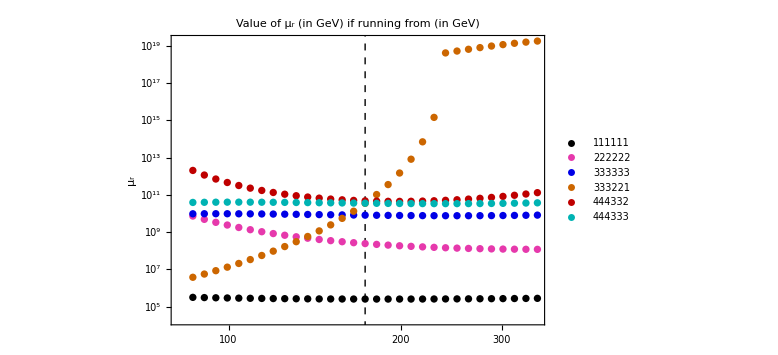

```mathematica
Qs=theorerr[[2;;32,1]];
ListLogLogPlot[{Table[{Qs[[i]],tTOmu@FindRoot[theorsols[1,1,1,1,1,1][[i,2]],{t,11}][[1,2]]},{i,1,Length@theorsols[1,1,1,1,1,1]}],
Table[{Qs[[i]],tTOmu@FindRoot[theorsols[2,2,2,2,2,2][[i,2]],{t,11}][[1,2]]},{i,1,Length@theorsols[2,2,2,2,2,2]}],
Table[{Qs[[i]],tTOmu@FindRoot[theorsols[3,3,3,3,3,3][[i,2]],{t,11}][[1,2]]},{i,1,Length@theorsols[3,3,3,3,3,3]}],
Table[{Qs[[i]],tTOmu@FindRoot[theorsols[3,3,3,2,2,1][[i,2]],{t,11}][[1,2]]},{i,1,Length@theorsols[3,3,3,2,2,1]}],
Table[{Qs[[i]],tTOmu@FindRoot[theorsols[4,4,4,3,3,2][[i,2]],{t,11}][[1,2]]},{i,1,Length@theorsols[4,4,4,3,3,2]}],
Table[{Qs[[i]],tTOmu@FindRoot[theorsols[4,4,4,3,3,3][[i,2]],{t,11}][[1,2]]},{i,1,Length@theorsols[4,4,4,3,3,3]}]},PlotStyle->{loopColor[1,1,1,1,1,1],loopColor[2,2,2,2,2,2],loopColor[3,3,3,3,3,3],loopColor[3,3,3,2,2,1],loopColor[4,4,4,3,3,2],loopColor[3,3,3,2,2,2],loopColor[4,4,4,3,3,3]},PlotLegends->{"111111","222222","333333","333221","444332","444333"},PlotRange->Full,Epilog->{Dashed,InfiniteLine[{Log@173.22,0},{0,1}]},FrameTicks -> {{Automatic,Automatic}, {Automatic, None}}, 
 PlotLabel ->  "Value of μ_r (in GeV) if running from  (in GeV)",  FrameLabel -> {"", "μ_r"}, Frame -> True, 
 LabelStyle -> {FontSize -> 18, FontFamily -> "Times"},ImageSize->Large]
Export["figures/theorroot.pdf",%]
```

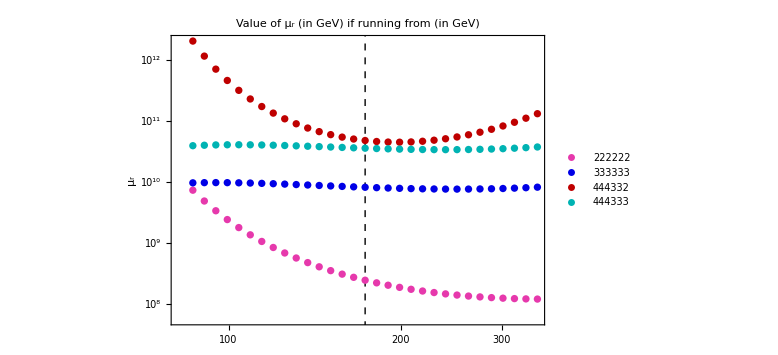

```mathematica
ListLogLogPlot[{
Table[{Qs[[i]],tTOmu@FindRoot[theorsols[2,2,2,2,2,2][[i,2]],{t,11}][[1,2]]},{i,1,Length@theorsols[2,2,2,2,2,2]}],
Table[{Qs[[i]],tTOmu@FindRoot[theorsols[3,3,3,3,3,3][[i,2]],{t,11}][[1,2]]},{i,1,Length@theorsols[3,3,3,3,3,3]}],
Table[{Qs[[i]],tTOmu@FindRoot[theorsols[4,4,4,3,3,2][[i,2]],{t,11}][[1,2]]},{i,1,Length@theorsols[4,4,4,3,3,2]}],
Table[{Qs[[i]],tTOmu@FindRoot[theorsols[4,4,4,3,3,3][[i,2]],{t,11}][[1,2]]},{i,1,Length@theorsols[4,4,4,3,3,3]}]},PlotStyle->{loopColor[2,2,2,2,2,2],loopColor[3,3,3,3,3,3],loopColor[4,4,4,3,3,2],loopColor[3,3,3,2,2,2],loopColor[4,4,4,3,3,3]},PlotLegends->{"222222","333333","444332","444333"},PlotRange->Full,Epilog->{Dashed,InfiniteLine[{Log@173.22,0},{0,1}]},FrameTicks -> {{Automatic,Automatic}, {Automatic, None}}, 
 PlotLabel ->  "Value of μ_r (in GeV) if running from  (in GeV)",  FrameLabel -> {"", "μ_r"}, Frame -> True, 
 LabelStyle -> {FontSize -> 18, FontFamily -> "Times"},ImageSize->Large]
Export["figures/theorrootless.pdf",%]
```

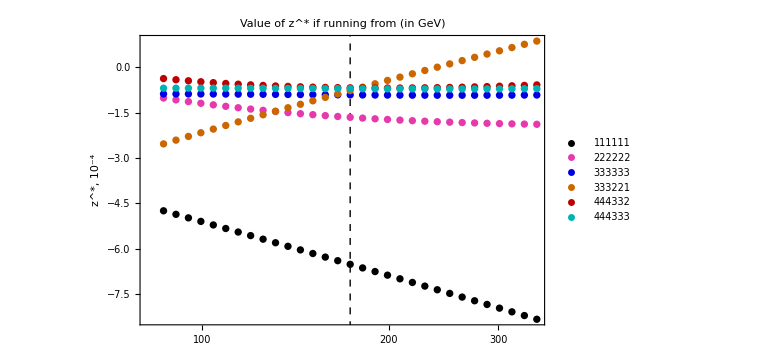

```mathematica
ListLogLinearPlot[{({#[[1]],10^(4) #[[2]]})&/@Table[{Qs[[i]],FindMinimum[{theorsols[1,1,1,1,1,1][[i,2]],10<=t<=80},{t,60}][[1]]},{i,1,Length@theorsols[1,1,1,1,1,1]}],
({#[[1]],10^(4) #[[2]]})&/@Table[{Qs[[i]],FindMinimum[{theorsols[2,2,2,2,2,2][[i,2]],10<=t<=80},{t,60}][[1]]},{i,1,Length@theorsols[2,2,2,2,2,2]}],
({#[[1]],10^(4) #[[2]]})&/@Table[{Qs[[i]],FindMinimum[{theorsols[3,3,3,3,3,3][[i,2]],10<=t<=80},{t,60}][[1]]},{i,1,Length@theorsols[3,3,3,3,3,3]}],
({#[[1]],10^(4) #[[2]]})&/@Table[{Qs[[i]],FindMinimum[{theorsols[3,3,3,2,2,1][[i,2]],10<=t<=80},{t,60}][[1]]},{i,1,Length@theorsols[3,3,3,2,2,1]}],
({#[[1]],10^(4) #[[2]]})&/@Table[{Qs[[i]],FindMinimum[{theorsols[4,4,4,3,3,2][[i,2]],10<=t<=80},{t,60}][[1]]},{i,1,Length@theorsols[4,4,4,3,3,2]}],
({#[[1]],10^(4) #[[2]]})&/@Table[{Qs[[i]],FindMinimum[{theorsols[4,4,4,3,3,3][[i,2]],10<=t<=80},{t,60}][[1]]},{i,1,Length@theorsols[4,4,4,3,3,3]}]},PlotStyle->{loopColor[1,1,1,1,1,1],loopColor[2,2,2,2,2,2],loopColor[3,3,3,3,3,3],loopColor[3,3,3,2,2,1],loopColor[4,4,4,3,3,2],loopColor[3,3,3,2,2,2],loopColor[4,4,4,3,3,3]},PlotLegends->{"111111","222222","333333","333221","444332","444333"},PlotRange->Full,Epilog->{Dashed,InfiniteLine[{Log@173.22,0},{0,1}]},FrameTicks -> {{Automatic,Automatic}, {Automatic, None}}, 
 PlotLabel ->  "Value of z^* if running from  (in GeV)",  FrameLabel -> {"", "z^*, 10^-4"}, Frame -> True, 
 LabelStyle -> {FontSize -> 18, FontFamily -> "Times"},ImageSize->Large]
Export["figures/theormin.pdf",%]
```

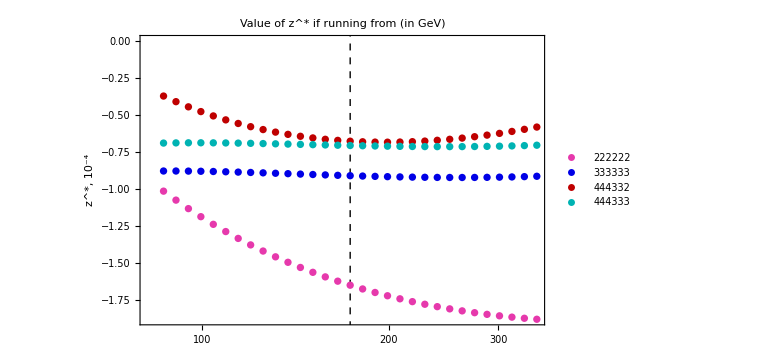

```mathematica
ListLogLinearPlot[{
({#[[1]],10^(4) #[[2]]})&/@Table[{Qs[[i]],FindMinimum[{theorsols[2,2,2,2,2,2][[i,2]],10<=t<=80},{t,60}][[1]]},{i,1,Length@theorsols[2,2,2,2,2,2]}],
({#[[1]],10^(4) #[[2]]})&/@Table[{Qs[[i]],FindMinimum[{theorsols[3,3,3,3,3,3][[i,2]],10<=t<=80},{t,60}][[1]]},{i,1,Length@theorsols[3,3,3,3,3,3]}],
({#[[1]],10^(4) #[[2]]})&/@Table[{Qs[[i]],FindMinimum[{theorsols[4,4,4,3,3,2][[i,2]],10<=t<=80},{t,60}][[1]]},{i,1,Length@theorsols[4,4,4,3,3,2]}],
({#[[1]],10^(4) #[[2]]})&/@Table[{Qs[[i]],FindMinimum[{theorsols[4,4,4,3,3,3][[i,2]],10<=t<=80},{t,60}][[1]]},{i,1,Length@theorsols[4,4,4,3,3,3]}]},PlotStyle->{loopColor[2,2,2,2,2,2],loopColor[3,3,3,3,3,3],loopColor[4,4,4,3,3,2],loopColor[3,3,3,2,2,2],loopColor[4,4,4,3,3,3]},PlotLegends->{"222222","333333","444332","444333"},PlotRange->Full,Epilog->{Dashed,InfiniteLine[{Log@173.22,0},{0,1}]},FrameTicks -> {{Automatic,Automatic}, {Automatic, None}}, 
 PlotLabel ->  "Value of z^* if running from  (in GeV)",  FrameLabel -> {"", "z^*, 10^-4"}, Frame -> True, 
 LabelStyle -> {FontSize -> 18, FontFamily -> "Times"},ImageSize->Large]
Export["figures/theorminless.pdf",%]
```

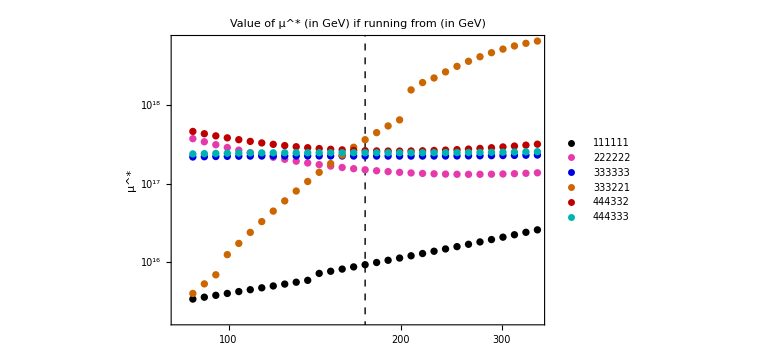

```mathematica
ListLogLogPlot[{Table[{Qs[[i]],tTOmu@FindMinimum[{theorsols[1,1,1,1,1,1][[i,2]],10<=t<=80},{t,60}][[2,1,2]]},{i,1,Length@theorsols[1,1,1,1,1,1]}],
Table[{Qs[[i]],tTOmu@FindMinimum[{theorsols[2,2,2,2,2,2][[i,2]],10<=t<=80},{t,60}][[2,1,2]]},{i,1,Length@theorsols[2,2,2,2,2,2]}],
Table[{Qs[[i]],tTOmu@FindMinimum[{theorsols[3,3,3,3,3,3][[i,2]],10<=t<=80},{t,60}][[2,1,2]]},{i,1,Length@theorsols[3,3,3,3,3,3]}],
Table[{Qs[[i]],tTOmu@FindMinimum[{theorsols[3,3,3,2,2,1][[i,2]],10<=t<=80},{t,60}][[2,1,2]]},{i,1,Length@theorsols[3,3,3,2,2,1]}],
Table[{Qs[[i]],tTOmu@FindMinimum[{theorsols[4,4,4,3,3,2][[i,2]],10<=t<=80},{t,60}][[2,1,2]]},{i,1,Length@theorsols[4,4,4,3,3,2]}],
Table[{Qs[[i]],tTOmu@FindMinimum[{theorsols[4,4,4,3,3,3][[i,2]],10<=t<=80},{t,60}][[2,1,2]]},{i,1,Length@theorsols[4,4,4,3,3,3]}]},PlotStyle->{loopColor[1,1,1,1,1,1],loopColor[2,2,2,2,2,2],loopColor[3,3,3,3,3,3],loopColor[3,3,3,2,2,1],loopColor[4,4,4,3,3,2],loopColor[3,3,3,2,2,2],loopColor[4,4,4,3,3,3]},PlotLegends->{"111111","222222","333333","333221","444332","444333"},PlotRange->Full,Epilog->{Dashed,InfiniteLine[{Log@173.22,0},{0,1}]},FrameTicks -> {{Automatic,Automatic}, {Automatic, None}}, 
 PlotLabel ->  "Value of μ^* (in GeV) if running from  (in GeV)",  FrameLabel -> {"", "μ^*"}, Frame -> True, 
 LabelStyle -> {FontSize -> 18, FontFamily -> "Times"},ImageSize->Large]
Export["figures/theormuofmin.pdf",%]
```

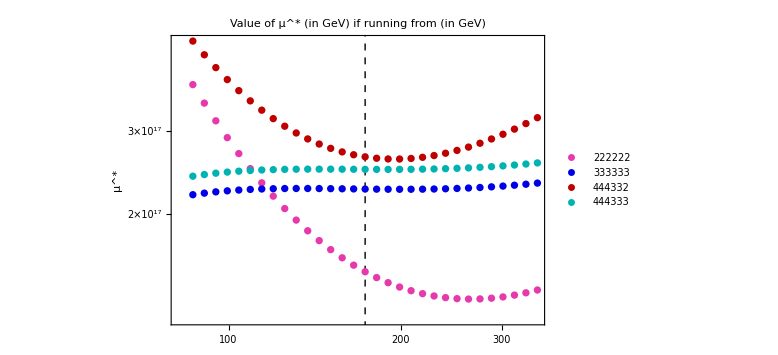

```mathematica
ListLogLogPlot[{
Table[{Qs[[i]],tTOmu@FindMinimum[{theorsols[2,2,2,2,2,2][[i,2]],10<=t<=80},{t,60}][[2,1,2]]},{i,1,Length@theorsols[2,2,2,2,2,2]}],
Table[{Qs[[i]],tTOmu@FindMinimum[{theorsols[3,3,3,3,3,3][[i,2]],10<=t<=80},{t,60}][[2,1,2]]},{i,1,Length@theorsols[3,3,3,3,3,3]}],
Table[{Qs[[i]],tTOmu@FindMinimum[{theorsols[4,4,4,3,3,2][[i,2]],10<=t<=80},{t,60}][[2,1,2]]},{i,1,Length@theorsols[4,4,4,3,3,2]}],
Table[{Qs[[i]],tTOmu@FindMinimum[{theorsols[4,4,4,3,3,3][[i,2]],10<=t<=80},{t,60}][[2,1,2]]},{i,1,Length@theorsols[4,4,4,3,3,3]}]},PlotStyle->{loopColor[2,2,2,2,2,2],loopColor[3,3,3,3,3,3],loopColor[4,4,4,3,3,2],loopColor[3,3,3,2,2,2],loopColor[4,4,4,3,3,3]},PlotLegends->{"222222","333333","444332","444333"},PlotRange->Full,Epilog->{Dashed,InfiniteLine[{Log@173.22,0},{0,1}]},FrameTicks -> {{Automatic,Automatic}, {Automatic, None}}, 
 PlotLabel ->  "Value of μ^* (in GeV) if running from  (in GeV)",  FrameLabel -> {"", "μ^*"}, Frame -> True, 
 LabelStyle -> {FontSize -> 18, FontFamily -> "Times"},ImageSize->Large]
Export["figures/theormuofminless.pdf",%]
```

## Final figures

```mathematica
loopCofigs={{1,1,1,1,1,1},{2,2,2,2,2,2},{3,3,3,3,3,3},{3,3,3,2,2,1},{4,4,4,3,3,2},{4,4,4,3,3,3}}
```

{{1,1,1,1,1,1},{2,2,2,2,2,2},{3,3,3,3,3,3},{3,3,3,2,2,1},{4,4,4,3,3,2},{4,4,4,3,3,3}}

```mathematica
paramColor=Blue;
paramErrort[x_,t_Around]:={Line[{{x+0.005,Log@tTOmu[t["Value"]-t["Uncertainty"]]},{x+0.005,Log@tTOmu[t["Value"]+t["Uncertainty"]]}}],Line[{{x+0.07,Log@tTOmu[t["Value"]-t["Uncertainty"]]},{x-0.07,Log@tTOmu[t["Value"]-t["Uncertainty"]]}}],Line[{{x+0.07,Log@tTOmu[t["Value"]+t["Uncertainty"]]},{x-0.07,Log@tTOmu[t["Value"]+t["Uncertainty"]]}}]}
paramErrorz[x_,z_Around]:={Line[{{x+0.001,z["Value"]-z["Uncertainty"]},{x+0.001,z["Value"]+z["Uncertainty"]}}],Line[{{x+0.07,z["Value"]-z["Uncertainty"]},{x-0.07,z["Value"]-z["Uncertainty"]}}],Line[{{x+0.07,z["Value"]+z["Uncertainty"]},{x-0.07,z["Value"]+z["Uncertainty"]}}]}

theorColor=Darker[Red];
theorErrort[x_,mint_,maxt_]:={Line[{{x-0.005,Log@tTOmu[mint]},{x-0.005,Log@tTOmu[maxt]}}],Line[{{x+0.07,Log@tTOmu[mint]},{x-0.07,Log@tTOmu[mint]}}],Line[{{x+0.07,Log@tTOmu[maxt]},{x-0.07,Log@tTOmu[maxt]}}]}
theorErrorz[x_,minz_,maxz_]:={Line[{{x-0.001,minz},{x,maxz}}],Line[{{x-0.001+0.07,minz},{x-0.07,minz}}],Line[{{x+0.07,maxz},{x-0.07,maxz}}]}

legendt[{xmin_,xmax_},{ymin_,ymax_}]:={
{EdgeForm[Thin],White, Rectangle[{xmin+0.65(xmax-xmin),Log[ymin]+0.13(Log[ymax]-Log[ymin])},{xmin+0.95(xmax-xmin),Log[ymin]+0.35(Log[ymax]-Log[ymin])}]},
{paramColor,theorErrort[xmin+0.69(xmax-xmin),muTOt[Exp[Log[ymin]+0.26(Log[ymax]-Log[ymin])]],muTOt[Exp[Log[ymin]+0.31(Log[ymax]-Log[ymin])]]]},
{theorColor,theorErrort[xmin+0.69(xmax-xmin),muTOt[Exp[Log[ymin]+0.16(Log[ymax]-Log[ymin])]],muTOt[Exp[Log[ymin]+0.21(Log[ymax]-Log[ymin])]]]},
Style[Text["Parametric unc.",{xmin+0.82(xmax-xmin),Log[ymin]+0.29(Log[ymax]-Log[ymin])}],FontSize -> 16,FontFamily->"Times"],
Style[Text["Theoretical unc.",{xmin+0.82(xmax-xmin),Log[ymin]+0.19(Log[ymax]-Log[ymin])}],FontSize -> 16,FontFamily->"Times"]
}
legendz[{xmin_,xmax_},{ymin_,ymax_}]:={
{EdgeForm[Thin],White, Rectangle[{xmin+0.65(xmax-xmin),ymin+0.13(ymax-ymin)},{xmin+0.95(xmax-xmin),ymin+0.35(ymax-ymin)}]},
{paramColor,theorErrorz[xmin+0.69(xmax-xmin),ymin+0.26(ymax-ymin),ymin+0.31(ymax-ymin)]},
{theorColor,theorErrorz[xmin+0.69(xmax-xmin),ymin+0.16(ymax-ymin),ymin+0.21(ymax-ymin)]},
Style[Text["Parametric unc.",{xmin+0.82(xmax-xmin),ymin+0.29(ymax-ymin)}],FontSize -> 16,FontFamily->"Times"],
Style[Text["Theoretical unc.",{xmin+0.82(xmax-xmin),ymin+0.19(ymax-ymin)}],FontSize -> 16,FontFamily->"Times"]
}
```

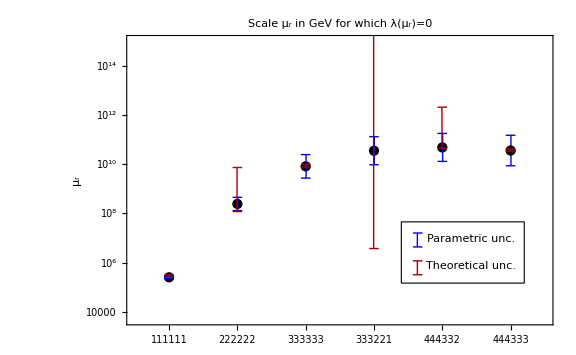

```mathematica
With[{xrange={0.5, 6.5},yrange={5*^3,  1*^15    }},ListLogPlot[
Table[{i,tTOmu[(theRoot@@loopCofigs[[i]])["Value"]]},{i,1,6}], FrameTicks -> {{Automatic,Automatic}, {{{1, "111111"}, {2, "222222"}, {3, "333333"}, {4, "333221"}, {5, "444332"}, {6, "444333"}}, None}}, 
 PlotLabel -> 
  "Scale μ_r in GeV for which λ(μ_r)=0", 
 FrameLabel -> {None, "μ_r"}, 
 PlotRange -> {xrange,yrange }, Frame -> True, 
 LabelStyle -> {FontSize -> 18, FontFamily -> "Times"}, ImageSize -> Large,PlotStyle->Black,
Epilog->Join[{
Join[{paramColor},Join@@Table[paramErrort[i,theRoot@@loopCofigs[[i]]],{i,1,6}]],
Join[{theorColor},Join@@Table[theorErrort[i,minRoot@@loopCofigs[[i]],maxRoot@@loopCofigs[[i]]],{i,1,6}]]
},legendt[xrange,yrange]]
]]
Export["figures/epicroots2.pdf",%]
```

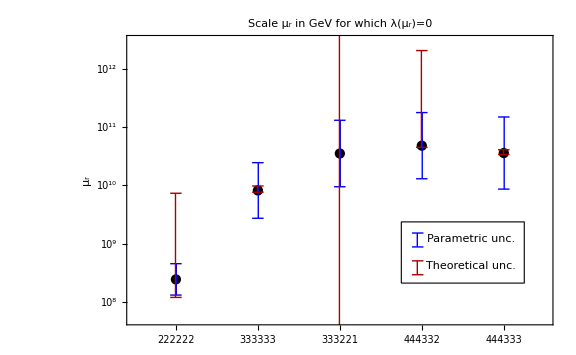

```mathematica
With[{xrange={1.5, 6.5},yrange={5*^7,  3*^12    }},ListLogPlot[
Table[{i,tTOmu[(theRoot@@loopCofigs[[i]])["Value"]]},{i,2,6}], FrameTicks -> {{Automatic,Automatic}, {{ {2, "222222"}, {3, "333333"}, {4, "333221"}, {5, "444332"}, {6, "444333"}}, None}}, 
 PlotLabel -> 
  "Scale μ_r in GeV for which λ(μ_r)=0", 
 FrameLabel -> {None, "μ_r"}, 
 PlotRange -> {xrange,yrange }, Frame -> True, 
 LabelStyle -> {FontSize -> 18, FontFamily -> "Times"}, ImageSize -> Large,PlotStyle->Black,
Epilog->Join[{
Join[{paramColor},Join@@Table[paramErrort[i,theRoot@@loopCofigs[[i]]],{i,1,6}]],
Join[{theorColor},Join@@Table[theorErrort[i,minRoot@@loopCofigs[[i]],maxRoot@@loopCofigs[[i]]],{i,1,6}]]
},legendt[xrange,yrange]]
]]
Export["figures/epicroots2less.pdf",%]
```

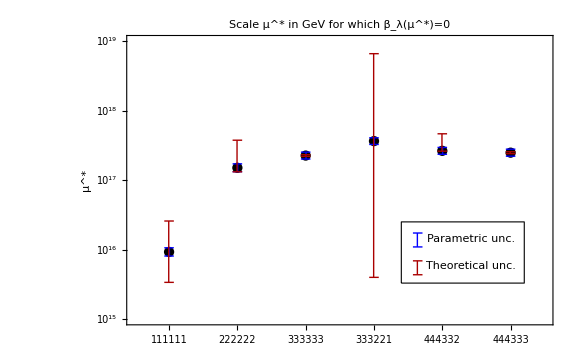

```mathematica
With[{xrange={0.5,6.5},yrange={10^15,10^19}},ListLogPlot[
Table[{i,tTOmu[(theTofMin@@loopCofigs[[i]])["Value"]]},{i,1,6}],PlotStyle->Black,FrameTicks->{{Automatic,Automatic},{{{1,"111111"},{2,"222222"},{3,"333333"},{4,"333221"},{5,"444332"},{6,"444333"}},None}},PlotLabel->"Scale μ^* in GeV for which β_λ(μ^*)=0",FrameLabel->{None,"μ^*"},PlotRange->{xrange,yrange},Frame->True,LabelStyle->{FontSize->18,FontFamily->"Times"},ImageSize->Large,
Epilog->Join[{
Join[{paramColor},Join@@Table[paramErrort[i,theTofMin@@loopCofigs[[i]]],{i,1,6}]],
Join[{theorColor},Join@@Table[theorErrort[i,minTofMin@@loopCofigs[[i]],maxTofMin@@loopCofigs[[i]]],{i,1,6}]]},legendt[xrange,yrange]]
]]
Export["figures/epicmuofmins.pdf",%]
```

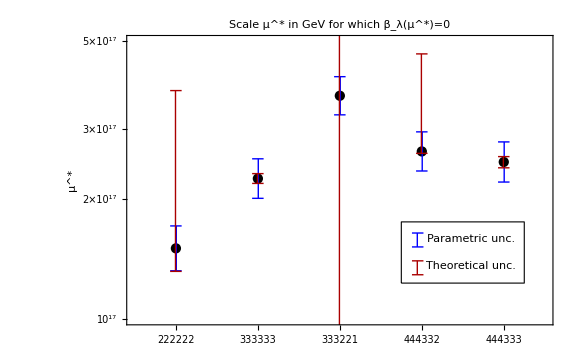

```mathematica
With[{xrange={1.5,6.5},yrange={1*^17,5*^17}},ListLogPlot[
Table[{i,tTOmu[(theTofMin@@loopCofigs[[i]])["Value"]]},{i,2,6}],PlotStyle->Black,FrameTicks->{{Automatic,Automatic},{{{2,"222222"},{3,"333333"},{4,"333221"},{5,"444332"},{6,"444333"}},None}},PlotLabel->"Scale μ^* in GeV for which β_λ(μ^*)=0",FrameLabel->{None,"μ^*"},PlotRange->{xrange,yrange},Frame->True,LabelStyle->{FontSize->18,FontFamily->"Times"},ImageSize->Large,
Epilog->Join[{
Join[{paramColor},Join@@Table[paramErrort[i,theTofMin@@loopCofigs[[i]]],{i,1,6}]],
Join[{theorColor},Join@@Table[theorErrort[i,minTofMin@@loopCofigs[[i]],maxTofMin@@loopCofigs[[i]]],{i,1,6}]]
},legendt[xrange,yrange]]
]]
Export["figures/epicmuofminsless.pdf",%]
```

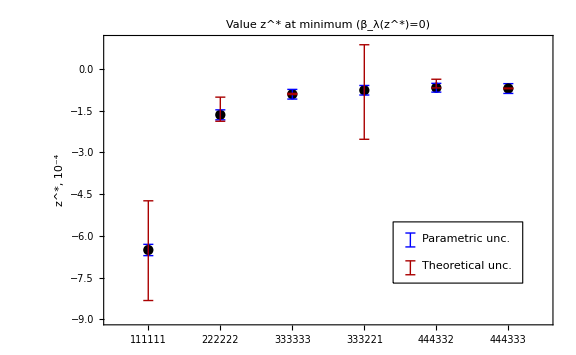

```mathematica
With[{xrange={0.5,6.5},yrange=10^(4){-0.0009,0.0001}},ListPlot[
Table[{i,10^(4)(theMin@@loopCofigs[[i]])["Value"]},{i,1,6}],FrameTicks->{{Automatic,Automatic},{{{1,"111111"},{2,"222222"},{3,"333333"},{4,"333221"},{5,"444332"},{6,"444333"}},None}},PlotLabel->"Value z^* at minimum (β_λ(z^*)=0)",FrameLabel->{None,"z^*, 10^-4"},PlotRange->{xrange,yrange},Frame->True,LabelStyle->{FontSize->18,FontFamily->"Times"},PlotStyle->Black,ImageSize->Large,
Epilog->Join[{
Join[{paramColor},Join@@Table[paramErrorz[i,10^(4) theMin@@loopCofigs[[i]]],{i,1,6}]],
Join[{theorColor},Join@@Table[theorErrorz[i,10^(4) minMin@@loopCofigs[[i]],10^(4) maxMin@@loopCofigs[[i]]],{i,1,6}]]
},legendz[xrange,yrange]]
]]
Export["figures/epicmins.pdf",%]
```

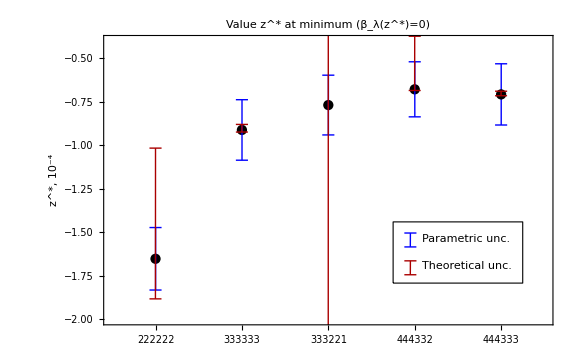

```mathematica
With[{xrange={1.5,6.5},yrange=10^(4){-0.0002,-0.00004}},ListPlot[
Table[{i,10^(4)(theMin@@loopCofigs[[i]])["Value"]},{i,2,6}],FrameTicks->{{Automatic,Automatic},{{{2,"222222"},{3,"333333"},{4,"333221"},{5,"444332"},{6,"444333"}},None}},PlotLabel->"Value z^* at minimum (β_λ(z^*)=0)",FrameLabel->{None,"z^*, 10^-4"},PlotRange->{xrange,yrange},Frame->True,LabelStyle->{FontSize->18,FontFamily->"Times"},PlotStyle->Black,ImageSize->Large,
Epilog->Join[{
Join[{paramColor},Join@@Table[paramErrorz[i,10^(4)theMin@@loopCofigs[[i]]],{i,1,6}]],
Join[{theorColor},Join@@Table[theorErrorz[i,10^(4)minMin@@loopCofigs[[i]],10^(4)maxMin@@loopCofigs[[i]]],{i,1,6}]]
},legendz[xrange,yrange]]
]]
Export["figures/epicminsless.pdf",%]
```

```mathematica
{{"tr",theRoot[1,1,1,1,1,1],theRoot[2,2,2,2,2,2],theRoot[3,3,3,3,3,3]},
{"μr",tTOmuWErrors[theRoot[1,1,1,1,1,1]],tTOmuWErrors[theRoot[2,2,2,2,2,2]],tTOmuWErrors[theRoot[3,3,3,3,3,3]]},
{"z*",theMin[1,1,1,1,1,1],theMin[2,2,2,2,2,2],theMin[3,3,3,3,3,3]},
{"t*",theTofMin[1,1,1,1,1,1],theTofMin[2,2,2,2,2,2],theTofMin[3,3,3,3,3,3]},
{"μ*",tTOmuWErrors[theTofMin[1,1,1,1,1,1]],tTOmuWErrors[theTofMin[2,2,2,2,2,2]],tTOmuWErrors[theTofMin[3,3,3,3,3,3]]}}//TableForm//TeXForm
```

\begin{array}{cccc}
 \text{tr} & 14.57\pm 0.25 & 28.3\pm 1.2 & 35.3\pm 2.2 \\
 \text{$\mu $r} & \left(2.53_{-0.30}^{+0.34}\right)\times 10^5 & \left(2.4_{-1.1}^{+2.1}\right)\times 10^8 & \left(0.8_{-0.5}^{+1.6}\right)\times 10^{10} \\
 \text{z*} & -0.000651\pm 0.000020 & -0.000165\pm 0.000018 & -0.000091\pm 0.000017 \\
 \text{t*} & 63.23\pm 0.27 & 68.80\pm 0.26 & 69.61\pm 0.23 \\
 \text{$\mu $*} & \left(9.3_{-1.2}^{+1.4}\right)\times 10^{15} & \left(1.51_{-0.18}^{+0.21}\right)\times 10^{17} & \left(2.26_{-0.24}^{+0.27}\right)\times 10^{17} \\
\end{array}

```mathematica
{{"tr",theRoot[3,3,3,2,2,1],theRoot[4,4,4,3,3,2],theRoot[4,4,4,3,3,3]},
{"μr",tTOmuWErrors[theRoot[3,3,3,2,2,1]],tTOmuWErrors[theRoot[4,4,4,3,3,2]],tTOmuWErrors[theRoot[4,4,4,3,3,3]]},
{"z*",theMin[3,3,3,2,2,1],theMin[4,4,4,3,3,2],theMin[4,4,4,3,3,3]},
{"t*",theTofMin[3,3,3,2,2,1],theTofMin[4,4,4,3,3,2],theTofMin[4,4,4,3,3,3]},
{"μ*",tTOmuWErrors[theTofMin[3,3,3,2,2,1]],tTOmuWErrors[theTofMin[4,4,4,3,3,2]],tTOmuWErrors[theTofMin[4,4,4,3,3,3]]}}//TableForm//TeXForm
```

\begin{array}{cccc}
 \text{tr} & 38.3\pm 2.6 & 38.9\pm 2.6 & 38.3\pm 2.8 \\
 \text{$\mu $r} & \left(3.5_{-2.6}^{+9.}\right)\times 10^{10} & \left(0.48_{-0.35}^{+1.3}\right)\times 10^{11} & \left(0.36_{-0.27}^{+1.1}\right)\times 10^{11} \\
 \text{z*} & -0.000077\pm 0.000017 & -0.000068\pm 0.000016 & -0.000071\pm 0.000017 \\
 \text{t*} & 70.56\pm 0.22 & 69.92\pm 0.23 & 69.80\pm 0.23 \\
 \text{$\mu $*} & \left(3.6_{-0.4}^{+0.4}\right)\times 10^{17} & \left(2.64_{-0.28}^{+0.32}\right)\times 10^{17} & \left(2.48_{-0.27}^{+0.31}\right)\times 10^{17} \\
\end{array}

```mathematica
{{"","μr max",tTOmu[maxRoot[1,1,1,1,1,1]],tTOmu[maxRoot[2,2,2,2,2,2]],tTOmu[maxRoot[3,3,3,3,3,3]]},{"multirow","μr min",tTOmu[minRoot[1,1,1,1,1,1]],tTOmu[minRoot[2,2,2,2,2,2]],tTOmu[minRoot[3,3,3,3,3,3]]},
{"","z* max",maxMin[1,1,1,1,1,1],maxMin[2,2,2,2,2,2],maxMin[3,3,3,3,3,3]},{"multirow","z* min",minMin[1,1,1,1,1,1],minMin[2,2,2,2,2,2],minMin[3,3,3,3,3,3]},{"","μ* max",tTOmu[maxTofMin[1,1,1,1,1,1]],tTOmu[maxTofMin[2,2,2,2,2,2]],tTOmu[maxTofMin[3,3,3,3,3,3]]},
{"multirow","μ* min",tTOmu[minTofMin[1,1,1,1,1,1]],tTOmu[minTofMin[2,2,2,2,2,2]],tTOmu[minTofMin[3,3,3,3,3,3]]}}//Map[toPower,#,{2}]&//TableForm//TeXForm
```

\begin{array}{ccccc}
 \text{} & \text{$\mu $r max} & 3.1224 \text{pow}(5) & 7.2999 \text{pow}(9) & 9.7304 \text{pow}(9) \\
 \text{multirow} & \text{$\mu $r min} & 2.5259 \text{pow}(5) & 1.1859 \text{pow}(8) & 7.6057 \text{pow}(9) \\
 \text{} & \text{z* max} & -4.7419 \text{pow}(-4) & -1.0157 \text{pow}(-4) & -8.794 \text{pow}(-5) \\
 \text{multirow} & \text{z* min} & -8.3263 \text{pow}(-4) & -1.8827 \text{pow}(-4) & -9.2327 \text{pow}(-5) \\
 \text{} & \text{$\mu $* max} & 2.5861 \text{pow}(16) & 3.7545 \text{pow}(17) & 2.3223 \text{pow}(17) \\
 \text{multirow} & \text{$\mu $* min} & 3.3925 \text{pow}(15) & 1.3191 \text{pow}(17) & 2.1944 \text{pow}(17) \\
\end{array}

```mathematica
{{"","μr max",tTOmu[maxRoot[3,3,3,2,2,1]],tTOmu[maxRoot[4,4,4,3,3,2]],tTOmu[maxRoot[4,4,4,3,3,3]]},{"multirow","μr min",tTOmu[minRoot[3,3,3,2,2,1]],tTOmu[minRoot[4,4,4,3,3,2]],tTOmu[minRoot[4,4,4,3,3,3]]},
{"","z* max",maxMin[3,3,3,2,2,1],maxMin[4,4,4,3,3,2],maxMin[4,4,4,3,3,3]},{"multirow","z* min",minMin[3,3,3,2,2,1],minMin[4,4,4,3,3,2],minMin[4,4,4,3,3,3]},{"","μ* max",tTOmu[maxTofMin[3,3,3,2,2,1]],tTOmu[maxTofMin[4,4,4,3,3,2]],tTOmu[maxTofMin[4,4,4,3,3,3]]},
{"multirow","μ* min",tTOmu[minTofMin[3,3,3,2,2,1]],tTOmu[minTofMin[4,4,4,3,3,2]],tTOmu[minTofMin[4,4,4,3,3,3]]}}//Map[toPower,#,{2}]&//TableForm//TeXForm
```

\begin{array}{ccccc}
 \text{} & \text{$\mu $r max} & 1.8429 \text{pow}(19) & 2.0612 \text{pow}(12) & 4.0764 \text{pow}(10) \\
 \text{multirow} & \text{$\mu $r min} & 3.7406 \text{pow}(6) & 4.4895 \text{pow}(10) & 3.3846 \text{pow}(10) \\
 \text{} & \text{z* max} & 8.6773 \text{pow}(-5) & -3.7212 \text{pow}(-5) & -6.8842 \text{pow}(-5) \\
 \text{multirow} & \text{z* min} & -2.5306 \text{pow}(-4) & -6.8426 \text{pow}(-5) & -7.1446 \text{pow}(-5) \\
 \text{} & \text{$\mu $* max} & 6.5858 \text{pow}(18) & 4.6423 \text{pow}(17) & 2.5625 \text{pow}(17) \\
 \text{multirow} & \text{$\mu $* min} & 4.004 \text{pow}(15) & 2.6115 \text{pow}(17) & 2.4016 \text{pow}(17) \\
\end{array}

## Probability

```mathematica
H0=1.44*^-42(*GeV*);
log10Atilde=1+5+7-2-38-14+25;
log10Prob[zmin_,TofMin_]:=Log10[0.15]+log10Atilde+4Log10[173.22/H0]+2Log10[E]TofMin-Log10[E] 1/(6Abs@zmin)
```

```mathematica
log10Prob[theMin[4,4,4,3,3,2],theTofMin[4,4,4,3,3,2]]
```

-848.250.

```mathematica
{Join[{"param"},Table[log10Prob[theMin@@loopCofigs[[i]],theTofMin@@loopCofigs[[i]]],{i,1,6}]],Join[{"theormax"},Table[Round@Min@Table[log10Prob@@(FindMinimum[{(theorsols@@loopCofigs[[i]])[[j,2]],10<=t<=80},{t,60}]//{#[[1]],#[[2,1,2]]}&),{j,1,Length@theorsols[1,1,1,1,1,1]}],{i,1,6}]],Join[{"theormin"},Table[Round@Max@Table[log10Prob@@(FindMinimum[{(theorsols@@loopCofigs[[i]])[[j,2]],10<=t<=80},{t,60}]//{#[[1]],#[[2,1,2]]}&),{j,1,Length@theorsols[1,1,1,1,1,1]}],{i,1,6}]]}//TableForm//TeXForm
```

\begin{array}{ccccccc}
 \text{param} & 103.2\pm 3.5 & -219.\pm 48. & -574.\pm 152. & -722.\pm 211. & -848.\pm 250. & -804.\pm 255. \\
 \text{theormax} & 60 & -492 & -603 & -163429 & -1724 & -831 \\
 \text{theormin} & 129 & -165 & -564 & -73 & -838 & -793 \\
\end{array}

```mathematica
{thelog10P[1,1,1,1,1,1],thelog10P[2,2,2,2,2,2],thelog10P[3,3,3,3,3,3],thelog10P[3,3,3,2,2,1],thelog10P[4,4,4,3,3,2],thelog10P[4,4,4,3,3,3]}=Table[log10Prob[theMin@@loopCofigs[[i]],theTofMin@@loopCofigs[[i]]],{i,1,6}];
{maxlog10P[1,1,1,1,1,1],maxlog10P[2,2,2,2,2,2],maxlog10P[3,3,3,3,3,3],maxlog10P[3,3,3,2,2,1],maxlog10P[4,4,4,3,3,2],maxlog10P[4,4,4,3,3,3]}=Table[Min@Table[log10Prob@@(FindMinimum[{(theorsols@@loopCofigs[[i]])[[j,2]],10<=t<=80},{t,60}]//{#[[1]],#[[2,1,2]]}&),{j,1,Length@theorsols[1,1,1,1,1,1]}],{i,1,6}];
{minlog10P[1,1,1,1,1,1],minlog10P[2,2,2,2,2,2],minlog10P[3,3,3,3,3,3],minlog10P[3,3,3,2,2,1],minlog10P[4,4,4,3,3,2],minlog10P[4,4,4,3,3,3]}=Table[Max@Table[log10Prob@@(FindMinimum[{(theorsols@@loopCofigs[[i]])[[j,2]],10<=t<=80},{t,60}]//{#[[1]],#[[2,1,2]]}&),{j,1,Length@theorsols[1,1,1,1,1,1]}],{i,1,6}];
```

```mathematica
legendP[{xmin_,xmax_},{ymin_,ymax_}]:={
{EdgeForm[Thin],White, Rectangle[{xmin+0.15(xmax-xmin),ymin+0.13(ymax-ymin)},{xmin+0.45(xmax-xmin),ymin+0.35(ymax-ymin)}]},
{paramColor,theorErrorz[xmin+0.19(xmax-xmin),ymin+0.26(ymax-ymin),ymin+0.31(ymax-ymin)]},
{theorColor,theorErrorz[xmin+0.19(xmax-xmin),ymin+0.16(ymax-ymin),ymin+0.21(ymax-ymin)]},
Style[Text["Parametric unc.",{xmin+0.32(xmax-xmin),ymin+0.29(ymax-ymin)}],FontSize -> 16,FontFamily->"Times"],
Style[Text["Theoretical unc.",{xmin+0.32(xmax-xmin),ymin+0.19(ymax-ymin)}],FontSize -> 16,FontFamily->"Times"]
}
```

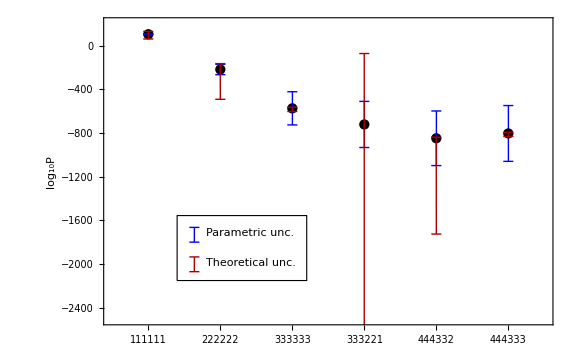

```mathematica
With[{xrange={0.5,6.5},yrange={-2500,200}},ListPlot[
Table[{i,(thelog10P@@loopCofigs[[i]])["Value"]},{i,1,6}],FrameTicks->{{Automatic,Automatic},{{{1,"111111"},{2,"222222"},{3,"333333"},{4,"333221"},{5,"444332"},{6,"444333"}},None}},PlotLabel->"",FrameLabel->{None,"log_10P"},PlotRange->{xrange,yrange},Frame->True,LabelStyle->{FontSize->18,FontFamily->"Times"},PlotStyle->Black,ImageSize->Large,
Epilog->Join[{
Join[{paramColor},Join@@Table[paramErrorz[i,thelog10P@@loopCofigs[[i]]],{i,1,6}]],
Join[{theorColor},Join@@Table[theorErrorz[i,minlog10P@@loopCofigs[[i]],maxlog10P@@loopCofigs[[i]]],{i,1,6}]]
},legendP[xrange,yrange]]
]]
Export["figures/epicPs.pdf",%]
```

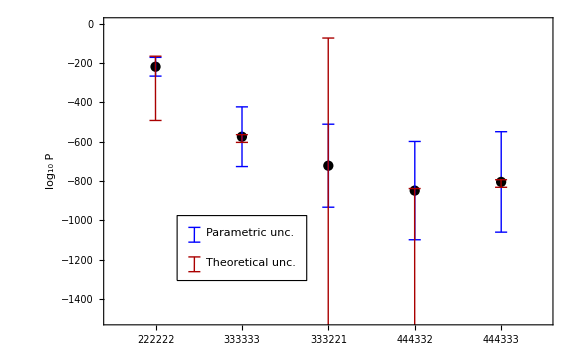

```mathematica
With[{xrange={1.5,6.5},yrange={-1500,0}},ListPlot[
Table[{i,(thelog10P@@loopCofigs[[i]])["Value"]},{i,2,6}],FrameTicks->{{Automatic,Automatic},{{{1,"111111"},{2,"222222"},{3,"333333"},{4,"333221"},{5,"444332"},{6,"444333"}},None}},PlotLabel->"",FrameLabel->{None,"log_10 P"},PlotRange->{xrange,yrange},Frame->True,LabelStyle->{FontSize->18,FontFamily->"Times"},PlotStyle->Black,ImageSize->Large,
Epilog->Join[{
Join[{paramColor},Join@@Table[paramErrorz[i,thelog10P@@loopCofigs[[i]]],{i,1,6}]],
Join[{theorColor},Join@@Table[theorErrorz[i,minlog10P@@loopCofigs[[i]],maxlog10P@@loopCofigs[[i]]],{i,1,6}]]
},legendP[xrange,yrange]]
]]
Export["figures/epicPsless.pdf",%]
```